```mathematica
ClearAll["Global`*"];
$Version
SetDirectory[NotebookDirectory[]];(*Mathematica file in the proper location*)
```

12.3.0 for Mac OS X x86 (64-bit) (May 10, 2021)

## Crossed-polarization (CP) optical microscopy intensity calculation

### A. Input

```mathematica
d=3.5;(*nm, CNC diameter*)
n1=1.33;(*water*)
n3=1.33; (*water*)
(*
Refractive index of cellulose crystal from Reference53: Chae I,et al.Anisotropic Optical and Frictional Properties of Langmuir–Blodgett Film Consisting of Uniaxially-Aligned Rod-Shaped Cellulose Nanocrystals.Advanced Materials Interfaces 7,(2020).
*)
nval=Import["nenodn.xlsx"];
Dimensions[nval]
nval//TableForm

ll=Table[nval[[1,i,1]],{i,2,17}];
nol=Table[nval[[1,i,2]],{i,2,17}];
nel=Table[nval[[1,i,3]],{i,2,17}];
```

{1,17,4}

lamda
no
ne
dn | 250.
1.55726
1.76155
0.20429 | 300.
1.52514
1.7146
0.18946 | 350.
1.50931
1.691
0.18169 | 400.
1.50001
1.67701
0.177 | 450.
1.494
1.66794
0.17394 | 500.
1.48986
1.66168
0.17182 | 550.
1.48688
1.65717
0.17029 | 600.
1.48466
1.6538
0.16914 | 650.
1.48295
1.65122
0.16827 | 700.
1.48161
1.64919
0.16758 | 750.
1.48055
1.64756
0.16701 | 800.
1.47968
1.64625
0.16657 | 850.
1.47896
1.64516
0.1662 | 900.
1.47836
1.64425
0.16589 | 950.
1.47786
1.64349
0.16563 | 1000.
1.47743
1.64284
0.16541

### B. Optical properties

CNC is considered as a thin film
-Graphics-

```mathematica
θ1=N[θ*π/180];(*rad*)

n2p=nel;
n2s=nol;

θ2p=ArcSin[n1 Sin[θ1]/n2p] ; (*Snell's law at the interface between 1 & 2*)
θ3p=ArcSin[n2p Sin[θ2p]/n3] ;(*Snell's law at the interface between 1 & 2*)
θ2s=ArcSin[n1 Sin[θ1]/n2s] ; (*Snell's law at the interface between 1 & 2*)
θ3s=ArcSin[n2s Sin[θ2s]/n3] ;(*Snell's law at the interface between 1 & 2*)

βp=(2 π)/ll d*n2p*Cos[θ2p] ;(* β=(2πd)/λ Subscript[n, 2]*cosθ - Equation 2 *)
βs=(2 π)/ll d*n2s*Cos[θ2s] ;(* β=(2πd)/λ Subscript[n, 2]*cosθ - Equation 2 *)

(*"thin film equations*)
t12p=(2*Cos[θ1]*Sin[θ2p])/(Sin[θ1+θ2p] Cos[θ1-θ2p]);

t12s=(2*Cos[θ1]*Sin[θ2s])/Sin[θ1+θ2s];

t23p=(2*Cos[θ2p]*Sin[θ3p])/(Sin[θ2p+θ3p] Cos[θ2p-θ3p]);

t23s=(2*Cos[θ2s]*Sin[θ3s])/Sin[θ2s+θ3s];

r12p=Tan[θ1-θ2p]/Tan[θ1+θ2p];

r12s=-Sin[θ1-θ2s]/Sin[θ1+θ2s];

r23p=Tan[θ2p-θ3p]/Tan[θ2p+θ3p];

r23s=-Sin[θ2s-θ3s]/Sin[θ2s+θ3s];

t123p=(t12p*t23p Exp[- I*βp])/(1+r12p*r23p Exp[-I*2 βp]);(* Subscript[t, 123]=(Subscript[t, 12]*Subscript[t, 23] Exp[-iβ])/(1+Subscript[r, 12]*Subscript[r, 23] Exp[-i2β]) - Equation 1 *)
t123s=(t12s*t23s Exp[- I*βs])/(1+r12s*r23s Exp[-I*2 βs]);(* Subscript[t, 123]=(Subscript[t, 12]*Subscript[t, 23] Exp[-iβ])/(1+Subscript[r, 12]*Subscript[r, 23] Exp[-i2β]) - Equation 1 *)

T123p=t123p*Conjugate[t123p];
T123s=t123s*Conjugate[t123s];
```

### C. Light properties after passing through a single CNC (add figure) - Electric field, intensity and polarization angle as a function of the polarization angle with respect to the CNC angle

(* Supplementary Figure 8a *)
Ep=E_‖, Es=E_⊥
-Graphics-

```mathematica
(*ϵ= ~0 *)
ϵ=10^-9;
θ=ϵ(*deg*);

(*Incident beam Ep0, Es0, Ip0, Is0*)
Ep0[ϕ_]:=1 Sin[ϕ*(π/180)];
Es0[ϕ_]:=1 Cos[ϕ*(π/180)];
Ip0[ϕ_]:=Ep0[ϕ]^2;
Is0[ϕ_]:=Es0[ϕ]^2;

(* Output beam- Ep1, Es1, Ip1, Is1 after a single CNC *)
Ep[ϕ_]:=Ep0[ϕ]*t123p[[8]];(*[[8]]=600nm *)
Es[ϕ_]:=Es0[ϕ]*t123s[[8]];(*[[8]]=600nm *)
Ip[ϕ_]:=Ep[ϕ]*Conjugate[Ep[ϕ]];
Is[ϕ_]:=Es[ϕ]*Conjugate[Es[ϕ]];

(* Output beam- ψ, (ψ-ϕ) (ϕ dependence) *)
ψ[ϕ_]:=Piecewise[{
{ArcTan[√(Ep[ϕ]*Conjugate[Ep[ϕ]])/√(Es[ϕ]*Conjugate[Es[ϕ]])]*180/π-180,ϕ<-90},
{ArcTan[√(Ep[ϕ]*Conjugate[Ep[ϕ]])/-√(Es[ϕ]*Conjugate[Es[ϕ]])]*180/π+180,ϕ>90},
{ArcTan[√(Ep[ϕ]*Conjugate[Ep[ϕ]])/√(Es[ϕ]*Conjugate[Es[ϕ]])]*180/π,ϕ>0},
{ArcTan[√(Ep[ϕ]*Conjugate[Ep[ϕ]])/-√(Es[ϕ]*Conjugate[Es[ϕ]])]*180/π,ϕ>-90}
}](* ψ=tan^-1[E_‖/E_⊥] - Equation 3 *)

(*Output beam |Etot| and Itot*)
Et[ϕ_]:=√(Ep[ϕ]*Conjugate[Ep[ϕ]]+Es[ϕ]*Conjugate[Es[ϕ]]);(* |Subscript[E, total]|=√(E_‖*E_‖^*+E_⊥*E_⊥^*) - Equation 4 *)
It[ϕ_]:=Et[ϕ]*Conjugate[Et[ϕ]];

(*transmission coefficient*)
tt[ϕ_]:=Et[ϕ]/1;
```

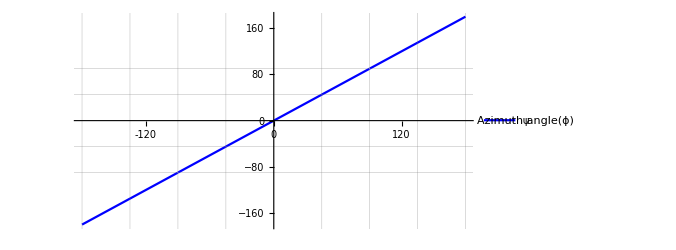
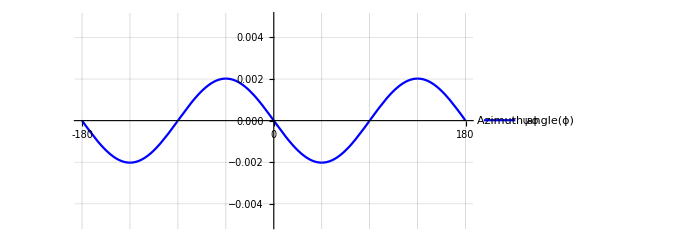

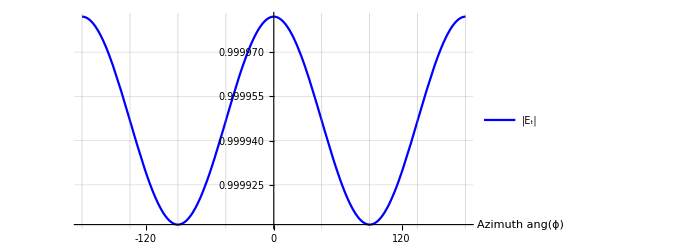
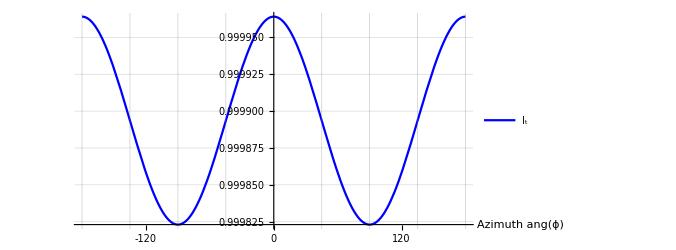

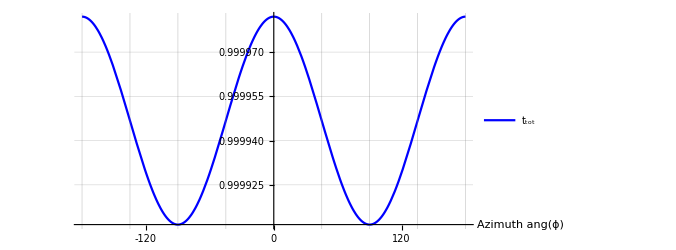

```mathematica
(*check plots*)
{Plot[ψ[ϕ],{ϕ,-180,180},PlotRange->{{-180,180},{-180,180}},Ticks->{Table[30i,{i,-12,12}], Automatic},GridLines->{Table[45i,{i,-4,4}], {-90,-45,45,90}},PlotLegends->Placed[{"ψ"},{0.7,0.9}],PlotStyle->{Blue},AxesLabel->{"Azimuth angle(ϕ)",None},ImageSize->500,AspectRatio->1/2,LabelStyle->{FontFamily->"Arial", FontSize->15,Black}],
Plot[{ψ[ϕ]-ϕ},{ϕ,-180,180},PlotRange->{{-180,180},{-0.005,0.005}},Ticks->{Table[45i,{i,-12,12}], Automatic},GridLines->{Table[45i,{i,-12,12}], Automatic},PlotLegends->Placed[{"ψ-ϕ"},{0.9,0.85}],PlotStyle->{Blue},AxesLabel->{"Azimuth angle(ϕ)",None},ImageSize->500,AspectRatio->1/2,LabelStyle->{FontFamily->"Arial", FontSize->15,Black}](* Supplementary Figure 8b *)
}

{Plot[Et[ϕ],{ϕ,-180,180},PlotRange->{{-180,180},All},Ticks->{Table[30i,{i,-12,12}], Automatic},GridLines->{Table[45i,{i,-12,12}], Automatic},PlotLegends->Placed[{"|E_t|"},{0.84,0.87}],PlotStyle->{Blue},AxesLabel->{"  Azimuth ang(ϕ)",None},ImageSize->500,AspectRatio->1/2,LabelStyle->{FontFamily->"Arial", FontSize->15,Black}](* Supplementary Figure 8c *),
Plot[It[ϕ],{ϕ,-180,180},PlotRange->{{-180,180},All},Ticks->{Table[30i,{i,-12,12}], Automatic},GridLines->{Table[45i,{i,-12,12}], Automatic},PlotLegends->Placed[{"I_t"},{0.84,0.87}],PlotStyle->{Blue},AxesLabel->{"  Azimuth ang(ϕ)",None},ImageSize->500,AspectRatio->1/2,LabelStyle->{FontFamily->"Arial", FontSize->15,Black}]}

Plot[tt[ϕ],{ϕ,-180,180},PlotRange->{{-180,180},All},Ticks->{Table[30i,{i,-12,12}], Automatic},GridLines->{Table[45i,{i,-12,12}], Automatic},PlotLegends->Placed[{"t_tot"},{0.84,0.87}],PlotStyle->{Blue},AxesLabel->{"  Azimuth ang(ϕ)",None},ImageSize->500,AspectRatio->1/2,LabelStyle->{FontFamily->"Arial", FontSize->15,Black}]
```

### D. 100 CNC angle generation for the five CMF organizations: crossed-polylamellate, random, helicoidal (10°), uniaxial, and biomodal.

```mathematica
n=100;(* number of CNCs (layers)*)
ϕ1=60; (* angle of the first CNC*)(*60 deg was chosen as an example - Supplementary Figure 8 *)
ϕ1=ϕ1;(* ϵ is a small number, 10^-9 *)

(*defined functions*)
F360[x_]:=x-Floor[x,360];
F180[x_]:=x-Floor[x,180];
F180off[x_]:=N[ArcSin[Sin[x*π/180]]*180/π];
F90off[x_]:=N[ArcCos[Cos[x*π/180]]*180/π];
```

(* Supplementary Figure 8d *)
Crossed-polylamellate structure as an example
-Graphics-

```mathematica
(* Crossed-polylamellate structure*)
ϕcl=Table[0,{i,1,n}];
ϕcl[[1]]=ϕ1;
dϕcl=Table[0,{i,1,n}];
dϕcl[[1]]=ϕ1;

For[i=1,i<n,i++,
ϕcl[[i+1]]=Round[ϕcl[[i]]+RandomVariate[NormalDistribution[61.9,15.4]]*(-1)^RandomInteger[{1,10}]];
dϕcl[[i+1]]=ϕcl[[i+1]]-ϕcl[[i]];
]

ϕcl;
ϕcl360=F360[ϕcl]
ϕcl180=F180[ϕcl];
ϕcl180Norm=F180[ϕcl180+90];
```

{60,328,261,189,102,137,187,132,200,146,223,145,53,22,293,232,283,230,287,242,179,119,182,250,309,226,277,181,250,311,353,279,223,174,218,162,231,169,119,174,211,148,78,114,59,1,290,351,271,331,276,358,53,346,56,3,71,149,204,249,321,23,84,7,68,121,185,123,176,236,275,191,125,69,23,333,14,76,30,308,258,314,239,154,87,27,70,131,214,117,155,125,53,351,321,269,331,32,328,267}

```mathematica
(* random orientation *)
ϕra=Round[RandomReal[{0,360},n]];
ϕra[[1]]=ϕ1;

dϕra=Table[0,{i,1,n}];
dϕra[[1]]=ϕ1;

For[i=1,i<n,i++,
dϕra[[i+1]]=ϕra[[i+1]]-ϕra[[i]];
]

ϕra;
ϕra360=F360[ϕra]
ϕra180=F180[ϕra];
ϕra180Norm=F180[ϕra180+90];
```

{60,185,51,58,288,286,231,63,65,115,231,73,129,159,154,250,54,296,256,310,242,139,122,301,297,71,65,69,55,19,339,136,160,181,281,46,170,36,172,25,175,145,21,47,240,301,256,19,137,6,261,22,303,333,143,63,75,323,264,28,8,165,13,113,268,342,112,307,331,137,130,345,91,288,187,288,191,235,337,140,64,88,13,271,130,22,192,216,157,301,315,144,7,218,323,109,222,297,94,103}

```mathematica
(* helicoidal 10° *)
ϕhe=Table[0,{i,1,n}];
ϕhe[[1]]=ϕ1;

For[i=1,i<n,i++,
ϕhe[[i+1]]=ϕhe[[i]]+10
]
ϕhe;
ϕhe360=F360[ϕhe]
ϕhe180=F180[ϕhe];
ϕhe180Norm=F180[ϕhe180+90];
```

{60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330}

```mathematica
(* uniaxial 10° *)
ϕun=Round[RandomVariate[NormalDistribution[90,10],n],1]
ϕun;
ϕun360=F360[ϕun];
ϕun180=F180[ϕun];
ϕun180Norm=F180[ϕun180+90];
```

{78,85,86,86,89,111,91,102,107,78,97,93,107,83,84,84,98,65,91,80,102,84,82,81,89,94,101,107,104,114,96,85,77,90,84,85,87,94,89,94,89,69,88,89,92,87,86,98,101,90,86,95,88,65,100,78,91,86,93,87,90,89,82,94,81,86,91,103,85,87,105,82,77,99,90,89,90,112,98,89,100,89,85,87,108,97,106,78,84,91,91,84,83,107,90,94,91,93,80,87}

```mathematica
(* bimodal ° *)
ϕbi=RandomVariate[MixtureDistribution[{1,1},{NormalDistribution[42,8],NormalDistribution[135,10]}],n];
ϕbi=Round[ϕbi,1]
ϕbi360=F360[ϕbi];
ϕbi180=F180[ϕbi];
ϕbi180Norm=F180[ϕbi180+90];
```

{29,21,149,41,46,36,123,126,40,31,136,50,41,44,139,145,40,116,34,149,38,49,138,119,146,137,134,154,51,130,128,142,128,39,131,141,132,141,138,145,34,134,130,120,45,34,40,143,48,146,39,139,138,45,46,28,32,124,46,37,35,142,43,37,134,132,143,35,29,56,121,129,132,34,48,39,145,130,41,134,45,126,52,138,127,22,139,136,123,53,113,51,154,128,31,41,42,146,135,41}

## E. Light properties after the 100 CNC organizations - Loop1 for each organization

```mathematica
ϕi=0;(* the initial polarization direction of the incident beam w.r.t. y-axis *)(*0 deg was chosen as an example - Supplementary Figure 8 *)
ϕi=ϕi+ϵ;(* ϵ is a small number, 10^-9 *)
```

### 1) Cross-polylamellate

#### Storage

```mathematica
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

Etot
ϕcl180

ψy
ϕbtn;
ψres;

dψ;
dψ2;
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{60,148,81,9,102,137,7,132,20,146,43,145,53,22,113,52,103,50,107,62,179,119,2,70,129,46,97,1,70,131,173,99,43,174,38,162,51,169,119,174,31,148,78,114,59,1,110,171,91,151,96,178,53,166,56,3,71,149,24,69,141,23,84,7,68,121,5,123,176,56,95,11,125,69,23,153,14,76,30,128,78,134,59,154,87,27,70,131,34,117,155,125,53,171,141,89,151,32,148,87}

{1.×10^-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Loop

```mathematica
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕcl180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕcl180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)
]
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕ1)*π/180])^2; (* I=(|Subscript[E, total]|*sinψ)^2 - Equation 5 *)
```

#### Check plots and final intensity (Supplementary Figure 8e,f here)

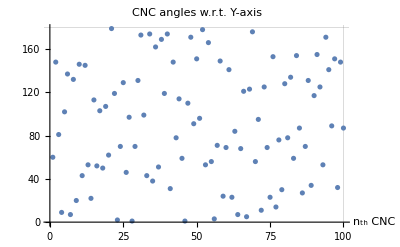
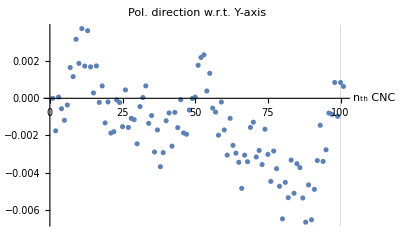
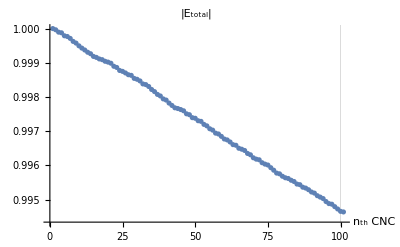
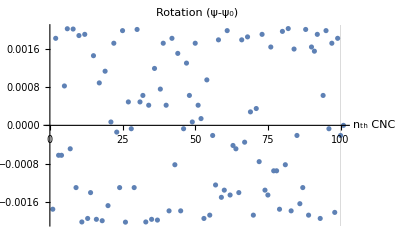

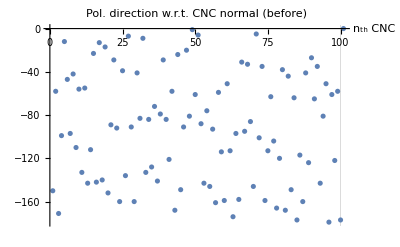
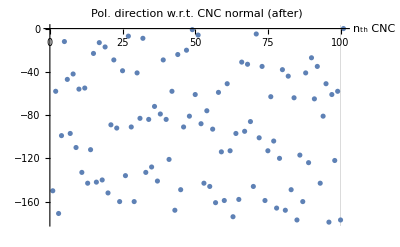

E_total after 100th CNC=0.994641+0. ⅈ

Final intensity after the 2nd polarizer=0.741974+0. ⅈ

```mathematica
{ListPlot[ϕcl180,ImageSize->400,PlotRange->All,AxesLabel->{"n_th CNC",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},GridLines->{{100},{180}},AxesOrigin->{0,0},PlotLabel->"CNC angles w.r.t. Y-axis"](* Supplementary Figure 8e *),
ListPlot[ψy,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. Y-axis",GridLines->{{100},None}](* Supplementary Figure 8f *),
ListPlot[Etot,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"|E_total|",GridLines->{{100},None}],
ListPlot[(dψ),ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Rotation (ψ-ψ_0)",GridLines->{{100},None}]}
{ListPlot[ϕbtn,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (before)",GridLines->{{100},None}],
ListPlot[ψres,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (after)",GridLines->{{100},None}]}

Print["E_total after 100th CNC=",Etot[[n+1]]]
Print["Final intensity after the 2nd polarizer=",PI]
```

#### Check numbers after each CNC

```mathematica
AppendTo[ϕcl180,0];
AppendTo[ϕcl180Norm,0];
ta1=Table[{i,ϕcl180[[i]],ψy[[i]],ϕcl180Norm[[i]],ϕbtn[[i]],ψres[[i]],dψ[[i]],"",ψy[[i]],dψ2[[i]]," ",Etot[[i]],ttot[[i]]},{i,1,n+1}];
PrependTo[ta1,{"nth CNC","CNC ang(180)","ψy","CNC norm ang","Ang btn(ϕbtn)","ψresult (CNC axis)","dψ(after-before)","+CNC norm","ψy","dψ2(ψ_(n + 1)-ψ_n)","-","E_tot","t_tot"}];
ta1//TableForm
```

nth CNC | CNC ang(180) | ψy | CNC norm ang | Ang btn(ϕbtn) | ψresult (CNC axis) | dψ(after-before) | +CNC norm | ψy | dψ2(ψ_(n + 1)-ψ_n) | - | E_tot | t_tot
1 | 60 | 1.×10^-9 | 150 | -150. | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 1.×10^-9 | -0.00174968+0. ⅈ |   | 1 | 0.999964+0. ⅈ
2 | 148 | -0.00174968+0. ⅈ | 58 | -58.0017+0. ⅈ | -57.9999+0. ⅈ | 0.00181589+0. ⅈ |  | -0.00174968+0. ⅈ | 0.00181589+0. ⅈ |   | 0.999964+0. ⅈ | 0.999931+0. ⅈ
3 | 81 | 0.0000662112+0. ⅈ | 171 | -171.+0. ⅈ | -171.001+0. ⅈ | -0.000624318+0. ⅈ |  | 0.0000662112+0. ⅈ | -0.000624318+0. ⅈ |   | 0.999896+0. ⅈ | 0.99998+0. ⅈ
4 | 9 | -0.000558107+0. ⅈ | 99 | -99.0006+0. ⅈ | -99.0012+0. ⅈ | -0.000624393+0. ⅈ |  | -0.000558107+0. ⅈ | -0.000624393+0. ⅈ |   | 0.999876+0. ⅈ | 0.999913+0. ⅈ
5 | 102 | -0.0011825+0. ⅈ | 12 | -12.0012+0. ⅈ | -12.0004+0. ⅈ | 0.000821816+0. ⅈ |  | -0.0011825+0. ⅈ | 0.000821816+0. ⅈ |   | 0.999789+0. ⅈ | 0.999979+0. ⅈ
6 | 137 | -0.000360684+0. ⅈ | 47 | -47.0004+0. ⅈ | -46.9983+0. ⅈ | 0.00201547+0. ⅈ |  | -0.000360684+0. ⅈ | 0.00201547+0. ⅈ |   | 0.999768+0. ⅈ | 0.999944+0. ⅈ
7 | 7 | 0.00165479+0. ⅈ | 97 | -96.9983+0. ⅈ | -96.9988+0. ⅈ | -0.00048868+0. ⅈ |  | 0.00165479+0. ⅈ | -0.00048868+0. ⅈ |   | 0.999713+0. ⅈ | 0.999913+0. ⅈ
8 | 132 | 0.00116611+0. ⅈ | 42 | -41.9988+0. ⅈ | -41.9968+0. ⅈ | 0.0020093+0. ⅈ |  | 0.00116611+0. ⅈ | 0.0020093+0. ⅈ |   | 0.999625+0. ⅈ | 0.99995+0. ⅈ
9 | 20 | 0.00317541+0. ⅈ | 110 | -109.997+0. ⅈ | -109.998+0. ⅈ | -0.00129854+0. ⅈ |  | 0.00317541+0. ⅈ | -0.00129854+0. ⅈ |   | 0.999576+0. ⅈ | 0.99992+0. ⅈ
10 | 146 | 0.00187687+0. ⅈ | 56 | -55.9981+0. ⅈ | -55.9962+0. ⅈ | 0.00187335+0. ⅈ |  | 0.00187687+0. ⅈ | 0.00187335+0. ⅈ |   | 0.999495+0. ⅈ | 0.999934+0. ⅈ
11 | 43 | 0.00375021+0. ⅈ | 133 | -132.996+0. ⅈ | -132.998+0. ⅈ | -0.00201545+0. ⅈ |  | 0.00375021+0. ⅈ | -0.00201545+0. ⅈ |   | 0.999429+0. ⅈ | 0.999944+0. ⅈ
12 | 145 | 0.00173476+0. ⅈ | 55 | -54.9983+0. ⅈ | -54.9964+0. ⅈ | 0.00189861+0. ⅈ |  | 0.00173476+0. ⅈ | 0.00189861+0. ⅈ |   | 0.999373+0. ⅈ | 0.999935+0. ⅈ
13 | 53 | 0.00363337+0. ⅈ | 143 | -142.996+0. ⅈ | -142.998+0. ⅈ | -0.00194217+0. ⅈ |  | 0.00363337+0. ⅈ | -0.00194217+0. ⅈ |   | 0.999308+0. ⅈ | 0.999956+0. ⅈ
14 | 22 | 0.00169119+0. ⅈ | 112 | -111.998+0. ⅈ | -112.+0. ⅈ | -0.00140343+0. ⅈ |  | 0.00169119+0. ⅈ | -0.00140343+0. ⅈ |   | 0.999265+0. ⅈ | 0.999921+0. ⅈ
15 | 113 | 0.000287765+0. ⅈ | 23 | -22.9997+0. ⅈ | -22.9983+0. ⅈ | 0.0014533+0. ⅈ |  | 0.000287765+0. ⅈ | 0.0014533+0. ⅈ |   | 0.999186+0. ⅈ | 0.999971+0. ⅈ
16 | 52 | 0.00174106+0. ⅈ | 142 | -141.998+0. ⅈ | -142.+0. ⅈ | -0.00196039+0. ⅈ |  | 0.00174106+0. ⅈ | -0.00196039+0. ⅈ |   | 0.999157+0. ⅈ | 0.999955+0. ⅈ
17 | 103 | -0.000219326+0. ⅈ | 13 | -13.0002+0. ⅈ | -12.9993+0. ⅈ | 0.000885666+0. ⅈ |  | -0.000219326+0. ⅈ | 0.000885666+0. ⅈ |   | 0.999113+0. ⅈ | 0.999978+0. ⅈ
18 | 50 | 0.00066634+0. ⅈ | 140 | -139.999+0. ⅈ | -140.001+0. ⅈ | -0.00198969+0. ⅈ |  | 0.00066634+0. ⅈ | -0.00198969+0. ⅈ |   | 0.999091+0. ⅈ | 0.999953+0. ⅈ
19 | 107 | -0.00132335+0. ⅈ | 17 | -17.0013+0. ⅈ | -17.0002+0. ⅈ | 0.00112983+0. ⅈ |  | -0.00132335+0. ⅈ | 0.00112983+0. ⅈ |   | 0.999044+0. ⅈ | 0.999976+0. ⅈ
20 | 62 | -0.000193519+0. ⅈ | 152 | -152.+0. ⅈ | -152.002+0. ⅈ | -0.00167494+0. ⅈ |  | -0.000193519+0. ⅈ | -0.00167494+0. ⅈ |   | 0.99902+0. ⅈ | 0.999966+0. ⅈ
21 | 179 | -0.00186846+0. ⅈ | 89 | -89.0019+0. ⅈ | -89.0018+0. ⅈ | 0.0000703813+0. ⅈ |  | -0.00186846+0. ⅈ | 0.0000703813+0. ⅈ |   | 0.998987+0. ⅈ | 0.999912+0. ⅈ
22 | 119 | -0.00179807+0. ⅈ | 29 | -29.0018+0. ⅈ | -29.0001+0. ⅈ | 0.00171342+0. ⅈ |  | -0.00179807+0. ⅈ | 0.00171342+0. ⅈ |   | 0.998898+0. ⅈ | 0.999965+0. ⅈ
23 | 2 | -0.0000846534+0. ⅈ | 92 | -92.0001+0. ⅈ | -92.0002+0. ⅈ | -0.000140946+0. ⅈ |  | -0.0000846534+0. ⅈ | -0.000140946+0. ⅈ |   | 0.998864+0. ⅈ | 0.999912+0. ⅈ
24 | 70 | -0.000225599+0. ⅈ | 160 | -160.+0. ⅈ | -160.002+0. ⅈ | -0.00129863+0. ⅈ |  | -0.000225599+0. ⅈ | -0.00129863+0. ⅈ |   | 0.998775+0. ⅈ | 0.999974+0. ⅈ
25 | 129 | -0.00152423+0. ⅈ | 39 | -39.0015+0. ⅈ | -38.9995+0. ⅈ | 0.00197625+0. ⅈ |  | -0.00152423+0. ⅈ | 0.00197625+0. ⅈ |   | 0.998749+0. ⅈ | 0.999954+0. ⅈ
26 | 46 | 0.000452013+0. ⅈ | 136 | -136.+0. ⅈ | -136.002+0. ⅈ | -0.00201916+0. ⅈ |  | 0.000452013+0. ⅈ | -0.00201916+0. ⅈ |   | 0.998703+0. ⅈ | 0.999948+0. ⅈ
27 | 97 | -0.00156714+0. ⅈ | 7 | -7.00157+0. ⅈ | -7.00108+0. ⅈ | 0.000488867+0. ⅈ |  | -0.00156714+0. ⅈ | 0.000488867+0. ⅈ |   | 0.998651+0. ⅈ | 0.999981+0. ⅈ
28 | 1 | -0.00107828+0. ⅈ | 91 | -91.0011+0. ⅈ | -91.0011+0. ⅈ | -0.000070589+0. ⅈ |  | -0.00107828+0. ⅈ | -0.000070589+0. ⅈ |   | 0.998632+0. ⅈ | 0.999912+0. ⅈ
29 | 70 | -0.00114887+0. ⅈ | 160 | -160.001+0. ⅈ | -160.002+0. ⅈ | -0.00129858+0. ⅈ |  | -0.00114887+0. ⅈ | -0.00129858+0. ⅈ |   | 0.998544+0. ⅈ | 0.999974+0. ⅈ
30 | 131 | -0.00244745+0. ⅈ | 41 | -41.0024+0. ⅈ | -41.0004+0. ⅈ | 0.00200074+0. ⅈ |  | -0.00244745+0. ⅈ | 0.00200074+0. ⅈ |   | 0.998518+0. ⅈ | 0.999952+0. ⅈ
31 | 173 | -0.000446709+0. ⅈ | 83 | -83.0004+0. ⅈ | -83.+0. ⅈ | 0.000488762+0. ⅈ |  | -0.000446709+0. ⅈ | 0.000488762+0. ⅈ |   | 0.99847+0. ⅈ | 0.999913+0. ⅈ
32 | 99 | 0.0000420537+0. ⅈ | 9 | -8.99996+0. ⅈ | -8.99933+0. ⅈ | 0.000624311+0. ⅈ |  | 0.0000420537+0. ⅈ | 0.000624311+0. ⅈ |   | 0.998382+0. ⅈ | 0.99998+0. ⅈ
33 | 43 | 0.000666364+0. ⅈ | 133 | -132.999+0. ⅈ | -133.001+0. ⅈ | -0.00201547+0. ⅈ |  | 0.000666364+0. ⅈ | -0.00201547+0. ⅈ |   | 0.998363+0. ⅈ | 0.999944+0. ⅈ
34 | 174 | -0.0013491+0. ⅈ | 84 | -84.0013+0. ⅈ | -84.0009+0. ⅈ | 0.000419984+0. ⅈ |  | -0.0013491+0. ⅈ | 0.000419984+0. ⅈ |   | 0.998307+0. ⅈ | 0.999912+0. ⅈ
35 | 38 | -0.00092912+0. ⅈ | 128 | -128.001+0. ⅈ | -128.003+0. ⅈ | -0.00196041+0. ⅈ |  | -0.00092912+0. ⅈ | -0.00196041+0. ⅈ |   | 0.99822+0. ⅈ | 0.999938+0. ⅈ
36 | 162 | -0.00288953+0. ⅈ | 72 | -72.0029+0. ⅈ | -72.0017+0. ⅈ | 0.00118742+0. ⅈ |  | -0.00288953+0. ⅈ | 0.00118742+0. ⅈ |   | 0.998158+0. ⅈ | 0.999918+0. ⅈ
37 | 51 | -0.0017021+0. ⅈ | 141 | -141.002+0. ⅈ | -141.004+0. ⅈ | -0.0019762+0. ⅈ |  | -0.0017021+0. ⅈ | -0.0019762+0. ⅈ |   | 0.998076+0. ⅈ | 0.999954+0. ⅈ
38 | 169 | -0.0036783+0. ⅈ | 79 | -79.0037+0. ⅈ | -79.0029+0. ⅈ | 0.000756635+0. ⅈ |  | -0.0036783+0. ⅈ | 0.000756635+0. ⅈ |   | 0.99803+0. ⅈ | 0.999914+0. ⅈ
39 | 119 | -0.00292167+0. ⅈ | 29 | -29.0029+0. ⅈ | -29.0012+0. ⅈ | 0.00171346+0. ⅈ |  | -0.00292167+0. ⅈ | 0.00171346+0. ⅈ |   | 0.997945+0. ⅈ | 0.999965+0. ⅈ
40 | 174 | -0.0012082+0. ⅈ | 84 | -84.0012+0. ⅈ | -84.0008+0. ⅈ | 0.000419993+0. ⅈ |  | -0.0012082+0. ⅈ | 0.000419993+0. ⅈ |   | 0.99791+0. ⅈ | 0.999912+0. ⅈ
41 | 31 | -0.00078821+0. ⅈ | 121 | -121.001+0. ⅈ | -121.003+0. ⅈ | -0.00178395+0. ⅈ |  | -0.00078821+0. ⅈ | -0.00178395+0. ⅈ |   | 0.997823+0. ⅈ | 0.99993+0. ⅈ
42 | 148 | -0.00257216+0. ⅈ | 58 | -58.0026+0. ⅈ | -58.0008+0. ⅈ | 0.00181586+0. ⅈ |  | -0.00257216+0. ⅈ | 0.00181586+0. ⅈ |   | 0.997753+0. ⅈ | 0.999931+0. ⅈ
43 | 78 | -0.000756301+0. ⅈ | 168 | -168.001+0. ⅈ | -168.002+0. ⅈ | -0.000821691+0. ⅈ |  | -0.000756301+0. ⅈ | -0.000821691+0. ⅈ |   | 0.997685+0. ⅈ | 0.999979+0. ⅈ
44 | 114 | -0.00157799+0. ⅈ | 24 | -24.0016+0. ⅈ | -24.0001+0. ⅈ | 0.00150148+0. ⅈ |  | -0.00157799+0. ⅈ | 0.00150148+0. ⅈ |   | 0.997664+0. ⅈ | 0.99997+0. ⅈ
45 | 59 | -0.0000765117+0. ⅈ | 149 | -149.+0. ⅈ | -149.002+0. ⅈ | -0.00178386+0. ⅈ |  | -0.0000765117+0. ⅈ | -0.00178386+0. ⅈ |   | 0.997634+0. ⅈ | 0.999963+0. ⅈ
46 | 1 | -0.00186038+0. ⅈ | 91 | -91.0019+0. ⅈ | -91.0019+0. ⅈ | -0.0000706441+0. ⅈ |  | -0.00186038+0. ⅈ | -0.0000706441+0. ⅈ |   | 0.997597+0. ⅈ | 0.999912+0. ⅈ
47 | 110 | -0.00193102+0. ⅈ | 20 | -20.0019+0. ⅈ | -20.0006+0. ⅈ | 0.00129875+0. ⅈ |  | -0.00193102+0. ⅈ | 0.00129875+0. ⅈ |   | 0.997509+0. ⅈ | 0.999974+0. ⅈ
48 | 171 | -0.000632271+0. ⅈ | 81 | -81.0006+0. ⅈ | -81.+0. ⅈ | 0.000624313+0. ⅈ |  | -0.000632271+0. ⅈ | 0.000624313+0. ⅈ |   | 0.997483+0. ⅈ | 0.999913+0. ⅈ
49 | 91 | -7.95815×10^-6+0. ⅈ | 1 | -1.00001+0. ⅈ | -0.999937+0. ⅈ | 0.0000705086+0. ⅈ |  | -7.95815×10^-6+0. ⅈ | 0.0000705086+0. ⅈ |   | 0.997396+0. ⅈ | 0.999982+0. ⅈ
50 | 151 | 0.0000625505+0. ⅈ | 61 | -60.9999+0. ⅈ | -60.9982+0. ⅈ | 0.00171342+0. ⅈ |  | 0.0000625505+0. ⅈ | 0.00171342+0. ⅈ |   | 0.997379+0. ⅈ | 0.999928+0. ⅈ
51 | 96 | 0.00177597+0. ⅈ | 6 | -5.99822+0. ⅈ | -5.9978+0. ⅈ | 0.000419925+0. ⅈ |  | 0.00177597+0. ⅈ | 0.000419925+0. ⅈ |   | 0.997307+0. ⅈ | 0.999981+0. ⅈ
52 | 178 | 0.0021959+0. ⅈ | 88 | -87.9978+0. ⅈ | -87.9977+0. ⅈ | 0.000141095+0. ⅈ |  | 0.0021959+0. ⅈ | 0.000141095+0. ⅈ |   | 0.997288+0. ⅈ | 0.999912+0. ⅈ
53 | 53 | 0.00233699+0. ⅈ | 143 | -142.998+0. ⅈ | -143.+0. ⅈ | -0.00194215+0. ⅈ |  | 0.00233699+0. ⅈ | -0.00194215+0. ⅈ |   | 0.9972+0. ⅈ | 0.999956+0. ⅈ
54 | 166 | 0.000394843+0. ⅈ | 76 | -75.9996+0. ⅈ | -75.9987+0. ⅈ | 0.000948569+0. ⅈ |  | 0.000394843+0. ⅈ | 0.000948569+0. ⅈ |   | 0.997157+0. ⅈ | 0.999916+0. ⅈ
55 | 56 | 0.00134341+0. ⅈ | 146 | -145.999+0. ⅈ | -146.001+0. ⅈ | -0.00187328+0. ⅈ |  | 0.00134341+0. ⅈ | -0.00187328+0. ⅈ |   | 0.997072+0. ⅈ | 0.99996+0. ⅈ
56 | 3 | -0.00052987+0. ⅈ | 93 | -93.0005+0. ⅈ | -93.0007+0. ⅈ | -0.000211233+0. ⅈ |  | -0.00052987+0. ⅈ | -0.000211233+0. ⅈ |   | 0.997033+0. ⅈ | 0.999912+0. ⅈ
57 | 71 | -0.000741103+0. ⅈ | 161 | -161.001+0. ⅈ | -161.002+0. ⅈ | -0.0012438+0. ⅈ |  | -0.000741103+0. ⅈ | -0.0012438+0. ⅈ |   | 0.996944+0. ⅈ | 0.999975+0. ⅈ
58 | 149 | -0.0019849+0. ⅈ | 59 | -59.002+0. ⅈ | -59.0002+0. ⅈ | 0.00178386+0. ⅈ |  | -0.0019849+0. ⅈ | 0.00178386+0. ⅈ |   | 0.996919+0. ⅈ | 0.99993+0. ⅈ
59 | 24 | -0.000201042+0. ⅈ | 114 | -114.+0. ⅈ | -114.002+0. ⅈ | -0.00150149+0. ⅈ |  | -0.000201042+0. ⅈ | -0.00150149+0. ⅈ |   | 0.99685+0. ⅈ | 0.999923+0. ⅈ
60 | 69 | -0.00170253+0. ⅈ | 159 | -159.002+0. ⅈ | -159.003+0. ⅈ | -0.00135178+0. ⅈ |  | -0.00170253+0. ⅈ | -0.00135178+0. ⅈ |   | 0.996773+0. ⅈ | 0.999973+0. ⅈ
61 | 141 | -0.00305431+0. ⅈ | 51 | -51.0031+0. ⅈ | -51.0011+0. ⅈ | 0.00197621+0. ⅈ |  | -0.00305431+0. ⅈ | 0.00197621+0. ⅈ |   | 0.996746+0. ⅈ | 0.999939+0. ⅈ
62 | 23 | -0.0010781+0. ⅈ | 113 | -113.001+0. ⅈ | -113.003+0. ⅈ | -0.00145343+0. ⅈ |  | -0.0010781+0. ⅈ | -0.00145343+0. ⅈ |   | 0.996686+0. ⅈ | 0.999922+0. ⅈ
63 | 84 | -0.00253153+0. ⅈ | 174 | -174.003+0. ⅈ | -174.003+0. ⅈ | -0.000419873+0. ⅈ |  | -0.00253153+0. ⅈ | -0.000419873+0. ⅈ |   | 0.996608+0. ⅈ | 0.999981+0. ⅈ
64 | 7 | -0.00295141+0. ⅈ | 97 | -97.003+0. ⅈ | -97.0034+0. ⅈ | -0.000488995+0. ⅈ |  | -0.00295141+0. ⅈ | -0.000488995+0. ⅈ |   | 0.99659+0. ⅈ | 0.999913+0. ⅈ
65 | 68 | -0.0034404+0. ⅈ | 158 | -158.003+0. ⅈ | -158.005+0. ⅈ | -0.00140327+0. ⅈ |  | -0.0034404+0. ⅈ | -0.00140327+0. ⅈ |   | 0.996502+0. ⅈ | 0.999972+0. ⅈ
66 | 121 | -0.00484367+0. ⅈ | 31 | -31.0048+0. ⅈ | -31.0031+0. ⅈ | 0.00178403+0. ⅈ |  | -0.00484367+0. ⅈ | 0.00178403+0. ⅈ |   | 0.996475+0. ⅈ | 0.999963+0. ⅈ
67 | 5 | -0.00305964+0. ⅈ | 95 | -95.0031+0. ⅈ | -95.0034+0. ⅈ | -0.000351061+0. ⅈ |  | -0.00305964+0. ⅈ | -0.000351061+0. ⅈ |   | 0.996438+0. ⅈ | 0.999912+0. ⅈ
68 | 123 | -0.0034107+0. ⅈ | 33 | -33.0034+0. ⅈ | -33.0016+0. ⅈ | 0.00184579+0. ⅈ |  | -0.0034107+0. ⅈ | 0.00184579+0. ⅈ |   | 0.99635+0. ⅈ | 0.999961+0. ⅈ
69 | 176 | -0.00156492+0. ⅈ | 86 | -86.0016+0. ⅈ | -86.0013+0. ⅈ | 0.000281084+0. ⅈ |  | -0.00156492+0. ⅈ | 0.000281084+0. ⅈ |   | 0.996312+0. ⅈ | 0.999912+0. ⅈ
70 | 56 | -0.00128383+0. ⅈ | 146 | -146.001+0. ⅈ | -146.003+0. ⅈ | -0.00187321+0. ⅈ |  | -0.00128383+0. ⅈ | -0.00187321+0. ⅈ |   | 0.996224+0. ⅈ | 0.99996+0. ⅈ
71 | 95 | -0.00315705+0. ⅈ | 5 | -5.00316+0. ⅈ | -5.00281+0. ⅈ | 0.000351044+0. ⅈ |  | -0.00315705+0. ⅈ | 0.000351044+0. ⅈ |   | 0.996184+0. ⅈ | 0.999981+0. ⅈ
72 | 11 | -0.002806+0. ⅈ | 101 | -101.003+0. ⅈ | -101.004+0. ⅈ | -0.000757059+0. ⅈ |  | -0.002806+0. ⅈ | -0.000757059+0. ⅈ |   | 0.996166+0. ⅈ | 0.999914+0. ⅈ
73 | 125 | -0.00356306+0. ⅈ | 35 | -35.0036+0. ⅈ | -35.0017+0. ⅈ | 0.00189861+0. ⅈ |  | -0.00356306+0. ⅈ | 0.00189861+0. ⅈ |   | 0.99608+0. ⅈ | 0.999959+0. ⅈ
74 | 69 | -0.00166445+0. ⅈ | 159 | -159.002+0. ⅈ | -159.003+0. ⅈ | -0.00135178+0. ⅈ |  | -0.00166445+0. ⅈ | -0.00135178+0. ⅈ |   | 0.996039+0. ⅈ | 0.999973+0. ⅈ
75 | 23 | -0.00301623+0. ⅈ | 113 | -113.003+0. ⅈ | -113.004+0. ⅈ | -0.00145353+0. ⅈ |  | -0.00301623+0. ⅈ | -0.00145353+0. ⅈ |   | 0.996012+0. ⅈ | 0.999922+0. ⅈ
76 | 153 | -0.00446976+0. ⅈ | 63 | -63.0045+0. ⅈ | -63.0028+0. ⅈ | 0.00163438+0. ⅈ |  | -0.00446976+0. ⅈ | 0.00163438+0. ⅈ |   | 0.995935+0. ⅈ | 0.999926+0. ⅈ
77 | 14 | -0.00283539+0. ⅈ | 104 | -104.003+0. ⅈ | -104.004+0. ⅈ | -0.000948721+0. ⅈ |  | -0.00283539+0. ⅈ | -0.000948721+0. ⅈ |   | 0.995861+0. ⅈ | 0.999916+0. ⅈ
78 | 76 | -0.00378411+0. ⅈ | 166 | -166.004+0. ⅈ | -166.005+0. ⅈ | -0.00094825+0. ⅈ |  | -0.00378411+0. ⅈ | -0.00094825+0. ⅈ |   | 0.995777+0. ⅈ | 0.999978+0. ⅈ
79 | 30 | -0.00473236+0. ⅈ | 120 | -120.005+0. ⅈ | -120.006+0. ⅈ | -0.00174991+0. ⅈ |  | -0.00473236+0. ⅈ | -0.00174991+0. ⅈ |   | 0.995755+0. ⅈ | 0.999929+0. ⅈ
80 | 128 | -0.00648226+0. ⅈ | 38 | -38.0065+0. ⅈ | -38.0045+0. ⅈ | 0.00196047+0. ⅈ |  | -0.00648226+0. ⅈ | 0.00196047+0. ⅈ |   | 0.995684+0. ⅈ | 0.999955+0. ⅈ
81 | 78 | -0.00452179+0. ⅈ | 168 | -168.005+0. ⅈ | -168.005+0. ⅈ | -0.000821448+0. ⅈ |  | -0.00452179+0. ⅈ | -0.000821448+0. ⅈ |   | 0.99564+0. ⅈ | 0.999979+0. ⅈ
82 | 134 | -0.00534324+0. ⅈ | 44 | -44.0053+0. ⅈ | -44.0033+0. ⅈ | 0.00201917+0. ⅈ |  | -0.00534324+0. ⅈ | 0.00201917+0. ⅈ |   | 0.995619+0. ⅈ | 0.999948+0. ⅈ
83 | 59 | -0.00332407+0. ⅈ | 149 | -149.003+0. ⅈ | -149.005+0. ⅈ | -0.00178376+0. ⅈ |  | -0.00332407+0. ⅈ | -0.00178376+0. ⅈ |   | 0.995567+0. ⅈ | 0.999963+0. ⅈ
84 | 154 | -0.00510783+0. ⅈ | 64 | -64.0051+0. ⅈ | -64.0035+0. ⅈ | 0.0015919+0. ⅈ |  | -0.00510783+0. ⅈ | 0.0015919+0. ⅈ |   | 0.995531+0. ⅈ | 0.999925+0. ⅈ
85 | 87 | -0.00351593+0. ⅈ | 177 | -177.004+0. ⅈ | -177.004+0. ⅈ | -0.000210934+0. ⅈ |  | -0.00351593+0. ⅈ | -0.000210934+0. ⅈ |   | 0.995456+0. ⅈ | 0.999982+0. ⅈ
86 | 27 | -0.00372687+0. ⅈ | 117 | -117.004+0. ⅈ | -117.005+0. ⅈ | -0.00163472+0. ⅈ |  | -0.00372687+0. ⅈ | -0.00163472+0. ⅈ |   | 0.995438+0. ⅈ | 0.999926+0. ⅈ
87 | 70 | -0.00536158+0. ⅈ | 160 | -160.005+0. ⅈ | -160.007+0. ⅈ | -0.00129836+0. ⅈ |  | -0.00536158+0. ⅈ | -0.00129836+0. ⅈ |   | 0.995364+0. ⅈ | 0.999974+0. ⅈ
88 | 131 | -0.00665994+0. ⅈ | 41 | -41.0067+0. ⅈ | -41.0047+0. ⅈ | 0.00200078+0. ⅈ |  | -0.00665994+0. ⅈ | 0.00200078+0. ⅈ |   | 0.995338+0. ⅈ | 0.999952+0. ⅈ
89 | 34 | -0.00465916+0. ⅈ | 124 | -124.005+0. ⅈ | -124.007+0. ⅈ | -0.00187342+0. ⅈ |  | -0.00465916+0. ⅈ | -0.00187342+0. ⅈ |   | 0.99529+0. ⅈ | 0.999934+0. ⅈ
90 | 117 | -0.00653258+0. ⅈ | 27 | -27.0065+0. ⅈ | -27.0049+0. ⅈ | 0.00163477+0. ⅈ |  | -0.00653258+0. ⅈ | 0.00163477+0. ⅈ |   | 0.995224+0. ⅈ | 0.999967+0. ⅈ
91 | 155 | -0.00489781+0. ⅈ | 65 | -65.0049+0. ⅈ | -65.0034+0. ⅈ | 0.00154752+0. ⅈ |  | -0.00489781+0. ⅈ | 0.00154752+0. ⅈ |   | 0.995192+0. ⅈ | 0.999924+0. ⅈ
92 | 125 | -0.00335029+0. ⅈ | 35 | -35.0034+0. ⅈ | -35.0015+0. ⅈ | 0.0018986+0. ⅈ |  | -0.00335029+0. ⅈ | 0.0018986+0. ⅈ |   | 0.995116+0. ⅈ | 0.999959+0. ⅈ
93 | 53 | -0.00145169+0. ⅈ | 143 | -143.001+0. ⅈ | -143.003+0. ⅈ | -0.00194207+0. ⅈ |  | -0.00145169+0. ⅈ | -0.00194207+0. ⅈ |   | 0.995075+0. ⅈ | 0.999956+0. ⅈ
94 | 171 | -0.00339376+0. ⅈ | 81 | -81.0034+0. ⅈ | -81.0028+0. ⅈ | 0.000624128+0. ⅈ |  | -0.00339376+0. ⅈ | 0.000624128+0. ⅈ |   | 0.995032+0. ⅈ | 0.999913+0. ⅈ
95 | 141 | -0.00276964+0. ⅈ | 51 | -51.0028+0. ⅈ | -51.0008+0. ⅈ | 0.00197621+0. ⅈ |  | -0.00276964+0. ⅈ | 0.00197621+0. ⅈ |   | 0.994945+0. ⅈ | 0.999939+0. ⅈ
96 | 89 | -0.000793423+0. ⅈ | 179 | -179.001+0. ⅈ | -179.001+0. ⅈ | -0.0000704521+0. ⅈ |  | -0.000793423+0. ⅈ | -0.0000704521+0. ⅈ |   | 0.994885+0. ⅈ | 0.999982+0. ⅈ
97 | 151 | -0.000863875+0. ⅈ | 61 | -61.0009+0. ⅈ | -60.9992+0. ⅈ | 0.00171339+0. ⅈ |  | -0.000863875+0. ⅈ | 0.00171339+0. ⅈ |   | 0.994867+0. ⅈ | 0.999928+0. ⅈ
98 | 32 | 0.000849511+0. ⅈ | 122 | -121.999+0. ⅈ | -122.001+0. ⅈ | -0.00181591+0. ⅈ |  | 0.000849511+0. ⅈ | -0.00181591+0. ⅈ |   | 0.994796+0. ⅈ | 0.999931+0. ⅈ
99 | 148 | -0.000966404+0. ⅈ | 58 | -58.001+0. ⅈ | -57.9992+0. ⅈ | 0.00181591+0. ⅈ |  | -0.000966404+0. ⅈ | 0.00181591+0. ⅈ |   | 0.994727+0. ⅈ | 0.999931+0. ⅈ
100 | 87 | 0.000849507+0. ⅈ | 177 | -176.999+0. ⅈ | -176.999+0. ⅈ | -0.00021124+0. ⅈ |  | 0.000849507+0. ⅈ | -0.00021124+0. ⅈ |   | 0.994659+0. ⅈ | 0.999982+0. ⅈ
101 | 0 | 0.000638267+0. ⅈ | 0 | 0 | 0 | 0 |  | 0.000638267+0. ⅈ | 0 |   | 0.994641+0. ⅈ | 0

### 2) Random

#### Storage

```mathematica
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

Etot
ϕra180

ψy
ϕbtn;
ψres;

dψ;
dψ2;
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{60,5,51,58,108,106,51,63,65,115,51,73,129,159,154,70,54,116,76,130,62,139,122,121,117,71,65,69,55,19,159,136,160,1,101,46,170,36,172,25,175,145,21,47,60,121,76,19,137,6,81,22,123,153,143,63,75,143,84,28,8,165,13,113,88,162,112,127,151,137,130,165,91,108,7,108,11,55,157,140,64,88,13,91,130,22,12,36,157,121,135,144,7,38,143,109,42,117,94,103}

{1.×10^-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Loop

```mathematica
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕra180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕra180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)
]
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕ1)*π/180])^2; (* I=(|Subscript[E, total]|*sinψ)^2 - Equation 5 *)
```

#### Check plots and final intensity

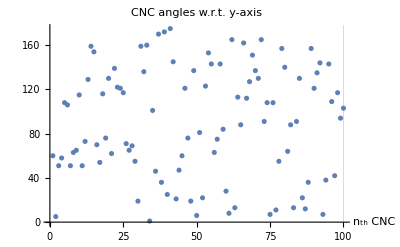
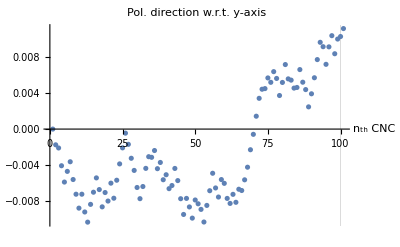
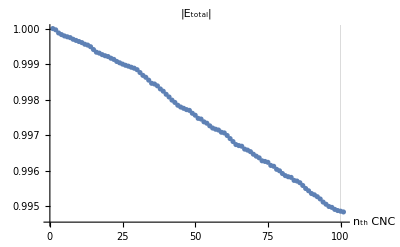
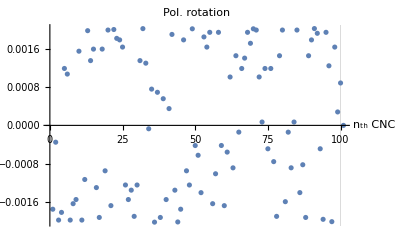

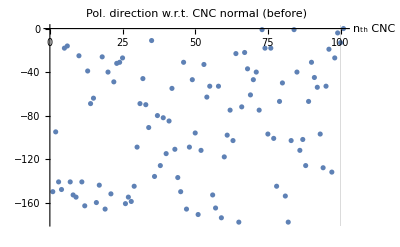
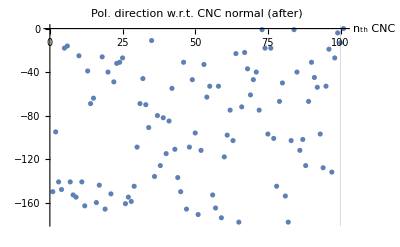

E_total after 100th CNC=0.994841+0. ⅈ

Final intensity after the 2nd polarizer=0.742114+0. ⅈ

```mathematica
{ListPlot[ϕra180,ImageSize->400,PlotRange->All,AxesLabel->{"n_th CNC",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},GridLines->{{100},{180}},AxesOrigin->{0,0},PlotLabel->"CNC angles w.r.t. y-axis"],
ListPlot[ψy,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. y-axis",GridLines->{{100},None}],
ListPlot[Etot,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"|E_total|",GridLines->{{100},None}],
ListPlot[(dψ),ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. rotation",GridLines->{{100},None}]}
{ListPlot[ϕbtn,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (before)",GridLines->{{100},None}],
ListPlot[ψres,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (after)",GridLines->{{100},None}]}

Print["E_total after 100th CNC=",Etot[[n+1]]]
Print["Final intensity after the 2nd polarizer=",PI]
```

#### Check numbers after each CNC

```mathematica
AppendTo[ϕra180,0];
AppendTo[ϕra180Norm,0];
ta1=Table[{i,ϕra180[[i]],ψy[[i]],ϕra180Norm[[i]],ϕbtn[[i]],ψres[[i]],dψ[[i]],"",ψy[[i]],dψ2[[i]]," ",Etot[[i]],ttot[[i]]},{i,1,n+1}];
PrependTo[ta1,{"nth CNC","CNC ang(180)","ψy","CNC norm ang","Ang btn(ϕbtn)","ψresult (CNC axis)","dψ(after-before)","+CNC norm","ψy","dψ2(ψ_(n + 1)-ψ_n)","-","E_tot","t_tot"}];
ta1//TableForm
```

nth CNC | CNC ang(180) | ψy | CNC norm ang | Ang btn(ϕbtn) | ψresult (CNC axis) | dψ(after-before) | +CNC norm | ψy | dψ2(ψ_(n + 1)-ψ_n) | - | E_tot | t_tot
1 | 60 | 1.×10^-9 | 150 | -150. | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 1.×10^-9 | -0.00174968+0. ⅈ |   | 1 | 0.999964+0. ⅈ
2 | 5 | -0.00174968+0. ⅈ | 95 | -95.0017+0. ⅈ | -95.0021+0. ⅈ | -0.00035097+0. ⅈ |  | -0.00174968+0. ⅈ | -0.00035097+0. ⅈ |   | 0.999964+0. ⅈ | 0.999912+0. ⅈ
3 | 51 | -0.00210065+0. ⅈ | 141 | -141.002+0. ⅈ | -141.004+0. ⅈ | -0.00197619+0. ⅈ |  | -0.00210065+0. ⅈ | -0.00197619+0. ⅈ |   | 0.999876+0. ⅈ | 0.999954+0. ⅈ
4 | 58 | -0.00407684+0. ⅈ | 148 | -148.004+0. ⅈ | -148.006+0. ⅈ | -0.00181576+0. ⅈ |  | -0.00407684+0. ⅈ | -0.00181576+0. ⅈ |   | 0.999831+0. ⅈ | 0.999962+0. ⅈ
5 | 108 | -0.0058926+0. ⅈ | 18 | -18.0059+0. ⅈ | -18.0047+0. ⅈ | 0.00118786+0. ⅈ |  | -0.0058926+0. ⅈ | 0.00118786+0. ⅈ |   | 0.999793+0. ⅈ | 0.999975+0. ⅈ
6 | 106 | -0.00470474+0. ⅈ | 16 | -16.0047+0. ⅈ | -16.0036+0. ⅈ | 0.00107089+0. ⅈ |  | -0.00470474+0. ⅈ | 0.00107089+0. ⅈ |   | 0.999768+0. ⅈ | 0.999977+0. ⅈ
7 | 51 | -0.00363385+0. ⅈ | 141 | -141.004+0. ⅈ | -141.006+0. ⅈ | -0.00197617+0. ⅈ |  | -0.00363385+0. ⅈ | -0.00197617+0. ⅈ |   | 0.999745+0. ⅈ | 0.999954+0. ⅈ
8 | 63 | -0.00561002+0. ⅈ | 153 | -153.006+0. ⅈ | -153.007+0. ⅈ | -0.00163426+0. ⅈ |  | -0.00561002+0. ⅈ | -0.00163426+0. ⅈ |   | 0.999699+0. ⅈ | 0.999968+0. ⅈ
9 | 65 | -0.00724428+0. ⅈ | 155 | -155.007+0. ⅈ | -155.009+0. ⅈ | -0.00154734+0. ⅈ |  | -0.00724428+0. ⅈ | -0.00154734+0. ⅈ |   | 0.999666+0. ⅈ | 0.999969+0. ⅈ
10 | 115 | -0.00879162+0. ⅈ | 25 | -25.0088+0. ⅈ | -25.0072+0. ⅈ | 0.00154807+0. ⅈ |  | -0.00879162+0. ⅈ | 0.00154807+0. ⅈ |   | 0.999636+0. ⅈ | 0.999969+0. ⅈ
11 | 51 | -0.00724355+0. ⅈ | 141 | -141.007+0. ⅈ | -141.009+0. ⅈ | -0.00197612+0. ⅈ |  | -0.00724355+0. ⅈ | -0.00197612+0. ⅈ |   | 0.999605+0. ⅈ | 0.999954+0. ⅈ
12 | 73 | -0.00921967+0. ⅈ | 163 | -163.009+0. ⅈ | -163.01+0. ⅈ | -0.00112921+0. ⅈ |  | -0.00921967+0. ⅈ | -0.00112921+0. ⅈ |   | 0.999559+0. ⅈ | 0.999976+0. ⅈ
13 | 129 | -0.0103489+0. ⅈ | 39 | -39.0103+0. ⅈ | -39.0084+0. ⅈ | 0.00197638+0. ⅈ |  | -0.0103489+0. ⅈ | 0.00197638+0. ⅈ |   | 0.999535+0. ⅈ | 0.999954+0. ⅈ
14 | 159 | -0.00837251+0. ⅈ | 69 | -69.0084+0. ⅈ | -69.007+0. ⅈ | 0.0013515+0. ⅈ |  | -0.00837251+0. ⅈ | 0.0013515+0. ⅈ |   | 0.99949+0. ⅈ | 0.999921+0. ⅈ
15 | 154 | -0.00702101+0. ⅈ | 64 | -64.007+0. ⅈ | -64.0054+0. ⅈ | 0.00159182+0. ⅈ |  | -0.00702101+0. ⅈ | 0.00159182+0. ⅈ |   | 0.99941+0. ⅈ | 0.999925+0. ⅈ
16 | 70 | -0.00542919+0. ⅈ | 160 | -160.005+0. ⅈ | -160.007+0. ⅈ | -0.00129835+0. ⅈ |  | -0.00542919+0. ⅈ | -0.00129835+0. ⅈ |   | 0.999335+0. ⅈ | 0.999974+0. ⅈ
17 | 54 | -0.00672755+0. ⅈ | 144 | -144.007+0. ⅈ | -144.009+0. ⅈ | -0.00192134+0. ⅈ |  | -0.00672755+0. ⅈ | -0.00192134+0. ⅈ |   | 0.999309+0. ⅈ | 0.999958+0. ⅈ
18 | 116 | -0.00864888+0. ⅈ | 26 | -26.0086+0. ⅈ | -26.0071+0. ⅈ | 0.00159243+0. ⅈ |  | -0.00864888+0. ⅈ | 0.00159243+0. ⅈ |   | 0.999267+0. ⅈ | 0.999968+0. ⅈ
19 | 76 | -0.00705645+0. ⅈ | 166 | -166.007+0. ⅈ | -166.008+0. ⅈ | -0.000948046+0. ⅈ |  | -0.00705645+0. ⅈ | -0.000948046+0. ⅈ |   | 0.999235+0. ⅈ | 0.999978+0. ⅈ
20 | 130 | -0.0080045+0. ⅈ | 40 | -40.008+0. ⅈ | -40.006+0. ⅈ | 0.00198978+0. ⅈ |  | -0.0080045+0. ⅈ | 0.00198978+0. ⅈ |   | 0.999213+0. ⅈ | 0.999953+0. ⅈ
21 | 62 | -0.00601472+0. ⅈ | 152 | -152.006+0. ⅈ | -152.008+0. ⅈ | -0.00167471+0. ⅈ |  | -0.00601472+0. ⅈ | -0.00167471+0. ⅈ |   | 0.999166+0. ⅈ | 0.999966+0. ⅈ
22 | 139 | -0.00768943+0. ⅈ | 49 | -49.0077+0. ⅈ | -49.0057+0. ⅈ | 0.00200066+0. ⅈ |  | -0.00768943+0. ⅈ | 0.00200066+0. ⅈ |   | 0.999133+0. ⅈ | 0.999942+0. ⅈ
23 | 122 | -0.00568877+0. ⅈ | 32 | -32.0057+0. ⅈ | -32.0039+0. ⅈ | 0.00181606+0. ⅈ |  | -0.00568877+0. ⅈ | 0.00181606+0. ⅈ |   | 0.999074+0. ⅈ | 0.999962+0. ⅈ
24 | 121 | -0.00387271+0. ⅈ | 31 | -31.0039+0. ⅈ | -31.0021+0. ⅈ | 0.001784+0. ⅈ |  | -0.00387271+0. ⅈ | 0.001784+0. ⅈ |   | 0.999037+0. ⅈ | 0.999963+0. ⅈ
25 | 117 | -0.00208871+0. ⅈ | 27 | -27.0021+0. ⅈ | -27.0005+0. ⅈ | 0.00163458+0. ⅈ |  | -0.00208871+0. ⅈ | 0.00163458+0. ⅈ |   | 0.999+0. ⅈ | 0.999967+0. ⅈ
26 | 71 | -0.000454128+0. ⅈ | 161 | -161.+0. ⅈ | -161.002+0. ⅈ | -0.00124382+0. ⅈ |  | -0.000454128+0. ⅈ | -0.00124382+0. ⅈ |   | 0.998968+0. ⅈ | 0.999975+0. ⅈ
27 | 65 | -0.00169794+0. ⅈ | 155 | -155.002+0. ⅈ | -155.003+0. ⅈ | -0.0015476+0. ⅈ |  | -0.00169794+0. ⅈ | -0.0015476+0. ⅈ |   | 0.998942+0. ⅈ | 0.999969+0. ⅈ
28 | 69 | -0.00324554+0. ⅈ | 159 | -159.003+0. ⅈ | -159.005+0. ⅈ | -0.0013517+0. ⅈ |  | -0.00324554+0. ⅈ | -0.0013517+0. ⅈ |   | 0.998912+0. ⅈ | 0.999973+0. ⅈ
29 | 55 | -0.00459724+0. ⅈ | 145 | -145.005+0. ⅈ | -145.006+0. ⅈ | -0.00189841+0. ⅈ |  | -0.00459724+0. ⅈ | -0.00189841+0. ⅈ |   | 0.998885+0. ⅈ | 0.999959+0. ⅈ
30 | 19 | -0.00649565+0. ⅈ | 109 | -109.006+0. ⅈ | -109.008+0. ⅈ | -0.00124427+0. ⅈ |  | -0.00649565+0. ⅈ | -0.00124427+0. ⅈ |   | 0.998844+0. ⅈ | 0.999919+0. ⅈ
31 | 159 | -0.00773992+0. ⅈ | 69 | -69.0077+0. ⅈ | -69.0064+0. ⅈ | 0.00135153+0. ⅈ |  | -0.00773992+0. ⅈ | 0.00135153+0. ⅈ |   | 0.998763+0. ⅈ | 0.999921+0. ⅈ
32 | 136 | -0.00638838+0. ⅈ | 46 | -46.0064+0. ⅈ | -46.0044+0. ⅈ | 0.00201914+0. ⅈ |  | -0.00638838+0. ⅈ | 0.00201914+0. ⅈ |   | 0.998683+0. ⅈ | 0.999946+0. ⅈ
33 | 160 | -0.00436924+0. ⅈ | 70 | -70.0044+0. ⅈ | -70.0031+0. ⅈ | 0.00129848+0. ⅈ |  | -0.00436924+0. ⅈ | 0.00129848+0. ⅈ |   | 0.998629+0. ⅈ | 0.99992+0. ⅈ
34 | 1 | -0.00307076+0. ⅈ | 91 | -91.0031+0. ⅈ | -91.0031+0. ⅈ | -0.0000707295+0. ⅈ |  | -0.00307076+0. ⅈ | -0.0000707295+0. ⅈ |   | 0.998549+0. ⅈ | 0.999912+0. ⅈ
35 | 101 | -0.00314149+0. ⅈ | 11 | -11.0031+0. ⅈ | -11.0024+0. ⅈ | 0.000757031+0. ⅈ |  | -0.00314149+0. ⅈ | 0.000757031+0. ⅈ |   | 0.99846+0. ⅈ | 0.999979+0. ⅈ
36 | 46 | -0.00238446+0. ⅈ | 136 | -136.002+0. ⅈ | -136.004+0. ⅈ | -0.00201915+0. ⅈ |  | -0.00238446+0. ⅈ | -0.00201915+0. ⅈ |   | 0.99844+0. ⅈ | 0.999948+0. ⅈ
37 | 170 | -0.00440361+0. ⅈ | 80 | -80.0044+0. ⅈ | -80.0037+0. ⅈ | 0.000690745+0. ⅈ |  | -0.00440361+0. ⅈ | 0.000690745+0. ⅈ |   | 0.998388+0. ⅈ | 0.999914+0. ⅈ
38 | 36 | -0.00371286+0. ⅈ | 126 | -126.004+0. ⅈ | -126.006+0. ⅈ | -0.00192161+0. ⅈ |  | -0.00371286+0. ⅈ | -0.00192161+0. ⅈ |   | 0.998302+0. ⅈ | 0.999936+0. ⅈ
39 | 172 | -0.00563447+0. ⅈ | 82 | -82.0056+0. ⅈ | -82.0051+0. ⅈ | 0.000556531+0. ⅈ |  | -0.00563447+0. ⅈ | 0.000556531+0. ⅈ |   | 0.998238+0. ⅈ | 0.999913+0. ⅈ
40 | 25 | -0.00507794+0. ⅈ | 115 | -115.005+0. ⅈ | -115.007+0. ⅈ | -0.00154797+0. ⅈ |  | -0.00507794+0. ⅈ | -0.00154797+0. ⅈ |   | 0.998151+0. ⅈ | 0.999924+0. ⅈ
41 | 175 | -0.00662591+0. ⅈ | 85 | -85.0066+0. ⅈ | -85.0063+0. ⅈ | 0.000350389+0. ⅈ |  | -0.00662591+0. ⅈ | 0.000350389+0. ⅈ |   | 0.998075+0. ⅈ | 0.999912+0. ⅈ
42 | 145 | -0.00627552+0. ⅈ | 55 | -55.0063+0. ⅈ | -55.0044+0. ⅈ | 0.00189842+0. ⅈ |  | -0.00627552+0. ⅈ | 0.00189842+0. ⅈ |   | 0.997987+0. ⅈ | 0.999935+0. ⅈ
43 | 21 | -0.00437711+0. ⅈ | 111 | -111.004+0. ⅈ | -111.006+0. ⅈ | -0.00135217+0. ⅈ |  | -0.00437711+0. ⅈ | -0.00135217+0. ⅈ |   | 0.997922+0. ⅈ | 0.999921+0. ⅈ
44 | 47 | -0.00572927+0. ⅈ | 137 | -137.006+0. ⅈ | -137.008+0. ⅈ | -0.00201543+0. ⅈ |  | -0.00572927+0. ⅈ | -0.00201543+0. ⅈ |   | 0.997843+0. ⅈ | 0.999949+0. ⅈ
45 | 60 | -0.00774471+0. ⅈ | 150 | -150.008+0. ⅈ | -150.009+0. ⅈ | -0.0017494+0. ⅈ |  | -0.00774471+0. ⅈ | -0.0017494+0. ⅈ |   | 0.997792+0. ⅈ | 0.999964+0. ⅈ
46 | 121 | -0.00949411+0. ⅈ | 31 | -31.0095+0. ⅈ | -31.0077+0. ⅈ | 0.00178418+0. ⅈ |  | -0.00949411+0. ⅈ | 0.00178418+0. ⅈ |   | 0.997757+0. ⅈ | 0.999963+0. ⅈ
47 | 76 | -0.00770993+0. ⅈ | 166 | -166.008+0. ⅈ | -166.009+0. ⅈ | -0.000948005+0. ⅈ |  | -0.00770993+0. ⅈ | -0.000948005+0. ⅈ |   | 0.99772+0. ⅈ | 0.999978+0. ⅈ
48 | 19 | -0.00865793+0. ⅈ | 109 | -109.009+0. ⅈ | -109.01+0. ⅈ | -0.00124439+0. ⅈ |  | -0.00865793+0. ⅈ | -0.00124439+0. ⅈ |   | 0.997698+0. ⅈ | 0.999919+0. ⅈ
49 | 137 | -0.00990233+0. ⅈ | 47 | -47.0099+0. ⅈ | -47.0079+0. ⅈ | 0.00201542+0. ⅈ |  | -0.00990233+0. ⅈ | 0.00201542+0. ⅈ |   | 0.997617+0. ⅈ | 0.999944+0. ⅈ
50 | 6 | -0.0078869+0. ⅈ | 96 | -96.0079+0. ⅈ | -96.0083+0. ⅈ | -0.000420621+0. ⅈ |  | -0.0078869+0. ⅈ | -0.000420621+0. ⅈ |   | 0.997562+0. ⅈ | 0.999912+0. ⅈ
51 | 81 | -0.00830752+0. ⅈ | 171 | -171.008+0. ⅈ | -171.009+0. ⅈ | -0.000623756+0. ⅈ |  | -0.00830752+0. ⅈ | -0.000623756+0. ⅈ |   | 0.997474+0. ⅈ | 0.99998+0. ⅈ
52 | 22 | -0.00893128+0. ⅈ | 112 | -112.009+0. ⅈ | -112.01+0. ⅈ | -0.00140397+0. ⅈ |  | -0.00893128+0. ⅈ | -0.00140397+0. ⅈ |   | 0.997454+0. ⅈ | 0.999921+0. ⅈ
53 | 123 | -0.0103352+0. ⅈ | 33 | -33.0103+0. ⅈ | -33.0085+0. ⅈ | 0.00184599+0. ⅈ |  | -0.0103352+0. ⅈ | 0.00184599+0. ⅈ |   | 0.997376+0. ⅈ | 0.999961+0. ⅈ
54 | 153 | -0.00848926+0. ⅈ | 63 | -63.0085+0. ⅈ | -63.0069+0. ⅈ | 0.00163421+0. ⅈ |  | -0.00848926+0. ⅈ | 0.00163421+0. ⅈ |   | 0.997337+0. ⅈ | 0.999926+0. ⅈ
55 | 143 | -0.00685505+0. ⅈ | 53 | -53.0069+0. ⅈ | -53.0049+0. ⅈ | 0.00194201+0. ⅈ |  | -0.00685505+0. ⅈ | 0.00194201+0. ⅈ |   | 0.997263+0. ⅈ | 0.999937+0. ⅈ
56 | 63 | -0.00491304+0. ⅈ | 153 | -153.005+0. ⅈ | -153.007+0. ⅈ | -0.00163429+0. ⅈ |  | -0.00491304+0. ⅈ | -0.00163429+0. ⅈ |   | 0.997201+0. ⅈ | 0.999967+0. ⅈ
57 | 75 | -0.00654733+0. ⅈ | 165 | -165.007+0. ⅈ | -165.008+0. ⅈ | -0.00100976+0. ⅈ |  | -0.00654733+0. ⅈ | -0.00100976+0. ⅈ |   | 0.997168+0. ⅈ | 0.999977+0. ⅈ
58 | 143 | -0.0075571+0. ⅈ | 53 | -53.0076+0. ⅈ | -53.0056+0. ⅈ | 0.00194199+0. ⅈ |  | -0.0075571+0. ⅈ | 0.00194199+0. ⅈ |   | 0.997146+0. ⅈ | 0.999937+0. ⅈ
59 | 84 | -0.0056151+0. ⅈ | 174 | -174.006+0. ⅈ | -174.006+0. ⅈ | -0.000419661+0. ⅈ |  | -0.0056151+0. ⅈ | -0.000419661+0. ⅈ |   | 0.997083+0. ⅈ | 0.999981+0. ⅈ
60 | 28 | -0.00603476+0. ⅈ | 118 | -118.006+0. ⅈ | -118.008+0. ⅈ | -0.00167525+0. ⅈ |  | -0.00603476+0. ⅈ | -0.00167525+0. ⅈ |   | 0.997064+0. ⅈ | 0.999927+0. ⅈ
61 | 8 | -0.00771001+0. ⅈ | 98 | -98.0077+0. ⅈ | -98.0083+0. ⅈ | -0.000557436+0. ⅈ |  | -0.00771001+0. ⅈ | -0.000557436+0. ⅈ |   | 0.996991+0. ⅈ | 0.999913+0. ⅈ
62 | 165 | -0.00826745+0. ⅈ | 75 | -75.0083+0. ⅈ | -75.0073+0. ⅈ | 0.00100972+0. ⅈ |  | -0.00826745+0. ⅈ | 0.00100972+0. ⅈ |   | 0.996905+0. ⅈ | 0.999916+0. ⅈ
63 | 13 | -0.00725773+0. ⅈ | 103 | -103.007+0. ⅈ | -103.008+0. ⅈ | -0.000886168+0. ⅈ |  | -0.00725773+0. ⅈ | -0.000886168+0. ⅈ |   | 0.996821+0. ⅈ | 0.999915+0. ⅈ
64 | 113 | -0.0081439+0. ⅈ | 23 | -23.0081+0. ⅈ | -23.0067+0. ⅈ | 0.00145371+0. ⅈ |  | -0.0081439+0. ⅈ | 0.00145371+0. ⅈ |   | 0.996736+0. ⅈ | 0.999971+0. ⅈ
65 | 88 | -0.00669019+0. ⅈ | 178 | -178.007+0. ⅈ | -178.007+0. ⅈ | -0.00014046+0. ⅈ |  | -0.00669019+0. ⅈ | -0.00014046+0. ⅈ |   | 0.996708+0. ⅈ | 0.999982+0. ⅈ
66 | 162 | -0.00683065+0. ⅈ | 72 | -72.0068+0. ⅈ | -72.0056+0. ⅈ | 0.0011872+0. ⅈ |  | -0.00683065+0. ⅈ | 0.0011872+0. ⅈ |   | 0.99669+0. ⅈ | 0.999918+0. ⅈ
67 | 112 | -0.00564345+0. ⅈ | 22 | -22.0056+0. ⅈ | -22.0042+0. ⅈ | 0.00140373+0. ⅈ |  | -0.00564345+0. ⅈ | 0.00140373+0. ⅈ |   | 0.996608+0. ⅈ | 0.999972+0. ⅈ
68 | 127 | -0.00423972+0. ⅈ | 37 | -37.0042+0. ⅈ | -37.0023+0. ⅈ | 0.00194219+0. ⅈ |  | -0.00423972+0. ⅈ | 0.00194219+0. ⅈ |   | 0.996581+0. ⅈ | 0.999956+0. ⅈ
69 | 151 | -0.00229753+0. ⅈ | 61 | -61.0023+0. ⅈ | -61.0006+0. ⅈ | 0.00171333+0. ⅈ |  | -0.00229753+0. ⅈ | 0.00171333+0. ⅈ |   | 0.996537+0. ⅈ | 0.999928+0. ⅈ
70 | 137 | -0.000584201+0. ⅈ | 47 | -47.0006+0. ⅈ | -46.9986+0. ⅈ | 0.00201547+0. ⅈ |  | -0.000584201+0. ⅈ | 0.00201547+0. ⅈ |   | 0.996466+0. ⅈ | 0.999944+0. ⅈ
71 | 130 | 0.00143127+0. ⅈ | 40 | -39.9986+0. ⅈ | -39.9966+0. ⅈ | 0.00198966+0. ⅈ |  | 0.00143127+0. ⅈ | 0.00198966+0. ⅈ |   | 0.99641+0. ⅈ | 0.999953+0. ⅈ
72 | 165 | 0.00342093+0. ⅈ | 75 | -74.9966+0. ⅈ | -74.9956+0. ⅈ | 0.00101043+0. ⅈ |  | 0.00342093+0. ⅈ | 0.00101043+0. ⅈ |   | 0.996363+0. ⅈ | 0.999916+0. ⅈ
73 | 91 | 0.00443137+0. ⅈ | 1 | -0.995569+0. ⅈ | -0.995498+0. ⅈ | 0.0000701957+0. ⅈ |  | 0.00443137+0. ⅈ | 0.0000701957+0. ⅈ |   | 0.99628+0. ⅈ | 0.999982+0. ⅈ
74 | 108 | 0.00450156+0. ⅈ | 18 | -17.9955+0. ⅈ | -17.9943+0. ⅈ | 0.00118726+0. ⅈ |  | 0.00450156+0. ⅈ | 0.00118726+0. ⅈ |   | 0.996262+0. ⅈ | 0.999975+0. ⅈ
75 | 7 | 0.00568883+0. ⅈ | 97 | -96.9943+0. ⅈ | -96.9948+0. ⅈ | -0.000488404+0. ⅈ |  | 0.00568883+0. ⅈ | -0.000488404+0. ⅈ |   | 0.996237+0. ⅈ | 0.999913+0. ⅈ
76 | 108 | 0.00520042+0. ⅈ | 18 | -17.9948+0. ⅈ | -17.9936+0. ⅈ | 0.00118722+0. ⅈ |  | 0.00520042+0. ⅈ | 0.00118722+0. ⅈ |   | 0.99615+0. ⅈ | 0.999975+0. ⅈ
77 | 11 | 0.00638765+0. ⅈ | 101 | -100.994+0. ⅈ | -100.994+0. ⅈ | -0.000756458+0. ⅈ |  | 0.00638765+0. ⅈ | -0.000756458+0. ⅈ |   | 0.996125+0. ⅈ | 0.999914+0. ⅈ
78 | 55 | 0.00563119+0. ⅈ | 145 | -144.994+0. ⅈ | -144.996+0. ⅈ | -0.00189866+0. ⅈ |  | 0.00563119+0. ⅈ | -0.00189866+0. ⅈ |   | 0.99604+0. ⅈ | 0.999959+0. ⅈ
79 | 157 | 0.00373253+0. ⅈ | 67 | -66.9963+0. ⅈ | -66.9948+0. ⅈ | 0.00145356+0. ⅈ |  | 0.00373253+0. ⅈ | 0.00145356+0. ⅈ |   | 0.995999+0. ⅈ | 0.999922+0. ⅈ
80 | 140 | 0.00518609+0. ⅈ | 50 | -49.9948+0. ⅈ | -49.9928+0. ⅈ | 0.00198977+0. ⅈ |  | 0.00518609+0. ⅈ | 0.00198977+0. ⅈ |   | 0.995921+0. ⅈ | 0.999941+0. ⅈ
81 | 64 | 0.00717586+0. ⅈ | 154 | -153.993+0. ⅈ | -153.994+0. ⅈ | -0.00159236+0. ⅈ |  | 0.00717586+0. ⅈ | -0.00159236+0. ⅈ |   | 0.995862+0. ⅈ | 0.999968+0. ⅈ
82 | 88 | 0.0055835+0. ⅈ | 178 | -177.994+0. ⅈ | -177.995+0. ⅈ | -0.000141323+0. ⅈ |  | 0.0055835+0. ⅈ | -0.000141323+0. ⅈ |   | 0.995831+0. ⅈ | 0.999982+0. ⅈ
83 | 13 | 0.00544218+0. ⅈ | 103 | -102.995+0. ⅈ | -102.995+0. ⅈ | -0.000885363+0. ⅈ |  | 0.00544218+0. ⅈ | -0.000885363+0. ⅈ |   | 0.995813+0. ⅈ | 0.999915+0. ⅈ
84 | 91 | 0.00455681+0. ⅈ | 1 | -0.995443+0. ⅈ | -0.995373+0. ⅈ | 0.0000701869+0. ⅈ |  | 0.00455681+0. ⅈ | 0.0000701869+0. ⅈ |   | 0.995728+0. ⅈ | 0.999982+0. ⅈ
85 | 130 | 0.004627+0. ⅈ | 40 | -39.9954+0. ⅈ | -39.9934+0. ⅈ | 0.00198963+0. ⅈ |  | 0.004627+0. ⅈ | 0.00198963+0. ⅈ |   | 0.99571+0. ⅈ | 0.999953+0. ⅈ
86 | 22 | 0.00661663+0. ⅈ | 112 | -111.993+0. ⅈ | -111.995+0. ⅈ | -0.00140318+0. ⅈ |  | 0.00661663+0. ⅈ | -0.00140318+0. ⅈ |   | 0.995663+0. ⅈ | 0.999921+0. ⅈ
87 | 12 | 0.00521345+0. ⅈ | 102 | -101.995+0. ⅈ | -101.996+0. ⅈ | -0.000821457+0. ⅈ |  | 0.00521345+0. ⅈ | -0.000821457+0. ⅈ |   | 0.995585+0. ⅈ | 0.999915+0. ⅈ
88 | 36 | 0.00439199+0. ⅈ | 126 | -125.996+0. ⅈ | -125.998+0. ⅈ | -0.00192143+0. ⅈ |  | 0.00439199+0. ⅈ | -0.00192143+0. ⅈ |   | 0.9955+0. ⅈ | 0.999936+0. ⅈ
89 | 157 | 0.00247056+0. ⅈ | 67 | -66.9975+0. ⅈ | -66.9961+0. ⅈ | 0.0014535+0. ⅈ |  | 0.00247056+0. ⅈ | 0.0014535+0. ⅈ |   | 0.995436+0. ⅈ | 0.999922+0. ⅈ
90 | 121 | 0.00392406+0. ⅈ | 31 | -30.9961+0. ⅈ | -30.9943+0. ⅈ | 0.00178374+0. ⅈ |  | 0.00392406+0. ⅈ | 0.00178374+0. ⅈ |   | 0.995359+0. ⅈ | 0.999963+0. ⅈ
91 | 135 | 0.0057078+0. ⅈ | 45 | -44.9943+0. ⅈ | -44.9923+0. ⅈ | 0.00202039+0. ⅈ |  | 0.0057078+0. ⅈ | 0.00202039+0. ⅈ |   | 0.995322+0. ⅈ | 0.999947+0. ⅈ
92 | 144 | 0.00772819+0. ⅈ | 54 | -53.9923+0. ⅈ | -53.9904+0. ⅈ | 0.00192169+0. ⅈ |  | 0.00772819+0. ⅈ | 0.00192169+0. ⅈ |   | 0.995269+0. ⅈ | 0.999936+0. ⅈ
93 | 7 | 0.00964988+0. ⅈ | 97 | -96.9904+0. ⅈ | -96.9908+0. ⅈ | -0.000488133+0. ⅈ |  | 0.00964988+0. ⅈ | -0.000488133+0. ⅈ |   | 0.995206+0. ⅈ | 0.999913+0. ⅈ
94 | 38 | 0.00916175+0. ⅈ | 128 | -127.991+0. ⅈ | -127.993+0. ⅈ | -0.00196023+0. ⅈ |  | 0.00916175+0. ⅈ | -0.00196023+0. ⅈ |   | 0.995119+0. ⅈ | 0.999938+0. ⅈ
95 | 143 | 0.00720152+0. ⅈ | 53 | -52.9928+0. ⅈ | -52.9909+0. ⅈ | 0.00194228+0. ⅈ |  | 0.00720152+0. ⅈ | 0.00194228+0. ⅈ |   | 0.995057+0. ⅈ | 0.999937+0. ⅈ
96 | 109 | 0.0091438+0. ⅈ | 19 | -18.9909+0. ⅈ | -18.9896+0. ⅈ | 0.00124333+0. ⅈ |  | 0.0091438+0. ⅈ | 0.00124333+0. ⅈ |   | 0.994995+0. ⅈ | 0.999975+0. ⅈ
97 | 42 | 0.0103871+0. ⅈ | 132 | -131.99+0. ⅈ | -131.992+0. ⅈ | -0.00200925+0. ⅈ |  | 0.0103871+0. ⅈ | -0.00200925+0. ⅈ |   | 0.994969+0. ⅈ | 0.999943+0. ⅈ
98 | 117 | 0.00837788+0. ⅈ | 27 | -26.9916+0. ⅈ | -26.99+0. ⅈ | 0.00163415+0. ⅈ |  | 0.00837788+0. ⅈ | 0.00163415+0. ⅈ |   | 0.994913+0. ⅈ | 0.999968+0. ⅈ
99 | 94 | 0.010012+0. ⅈ | 4 | -3.98999+0. ⅈ | -3.98971+0. ⅈ | 0.000280475+0. ⅈ |  | 0.010012+0. ⅈ | 0.000280475+0. ⅈ |   | 0.99488+0. ⅈ | 0.999982+0. ⅈ
100 | 103 | 0.0102925+0. ⅈ | 13 | -12.9897+0. ⅈ | -12.9888+0. ⅈ | 0.000884999+0. ⅈ |  | 0.0102925+0. ⅈ | 0.000884999+0. ⅈ |   | 0.994862+0. ⅈ | 0.999978+0. ⅈ
101 | 0 | 0.0111775+0. ⅈ | 0 | 0 | 0 | 0 |  | 0.0111775+0. ⅈ | 0 |   | 0.994841+0. ⅈ | 0

### 3) Helicoidal

#### Storage

```mathematica
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

Etot
ϕhe180

ψy
ϕbtn;
ψres;

dψ;
dψ2;
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150}

{1.×10^-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Loop

```mathematica
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕhe180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕhe180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)
]
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕ1)*π/180])^2; (* I=(|Subscript[E, total]|*sinψ)^2 - Equation 5 *)
```

#### Check plots and final intensity

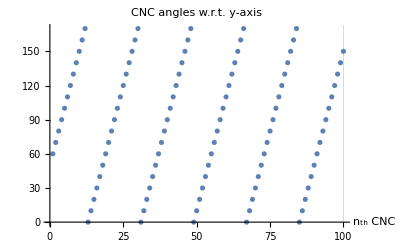
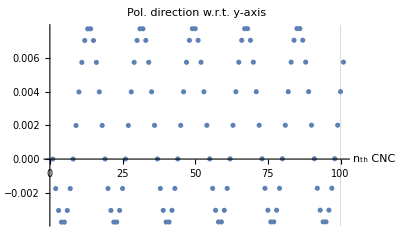
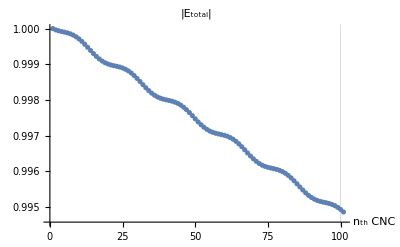
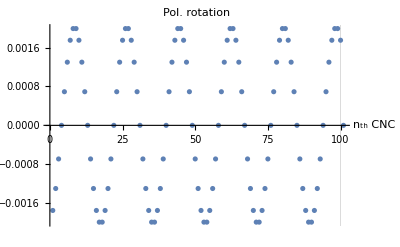

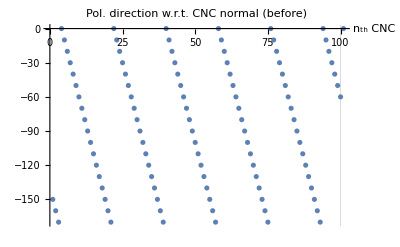
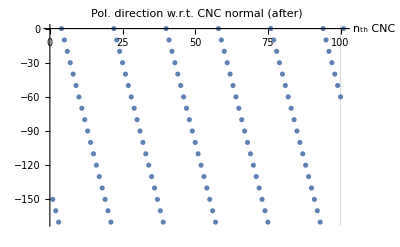

E_total after 100th CNC=0.994863+0. ⅈ

Final intensity after the 2nd polarizer=0.742228+0. ⅈ

```mathematica
{ListPlot[ϕhe180,ImageSize->400,PlotRange->All,AxesLabel->{"n_th CNC",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},GridLines->{{100},{180}},AxesOrigin->{0,0},PlotLabel->"CNC angles w.r.t. y-axis"],
ListPlot[ψy,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. y-axis",GridLines->{{100},None}],
ListPlot[Etot,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"|E_total|",GridLines->{{100},None}],
ListPlot[(dψ),ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. rotation",GridLines->{{100},None}]}
{ListPlot[ϕbtn,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (before)",GridLines->{{100},None}],
ListPlot[ψres,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (after)",GridLines->{{100},None}]}

Print["E_total after 100th CNC=",Etot[[n+1]]]
Print["Final intensity after the 2nd polarizer=",PI]
```

#### Check numbers after each CNC

```mathematica
AppendTo[ϕhe180,0];
AppendTo[ϕhe180Norm,0];
ta1=Table[{i,ϕhe180[[i]],ψy[[i]],ϕhe180Norm[[i]],ϕbtn[[i]],ψres[[i]],dψ[[i]],"",ψy[[i]],dψ2[[i]]," ",Etot[[i]],ttot[[i]]},{i,1,n+1}];
PrependTo[ta1,{"nth CNC","CNC ang(180)","ψy","CNC norm ang","Ang btn(ϕbtn)","ψresult (CNC axis)","dψ(after-before)","+CNC norm","ψy","dψ2(ψ_(n + 1)-ψ_n)","-","E_tot","t_tot"}];
ta1//TableForm
```

nth CNC | CNC ang(180) | ψy | CNC norm ang | Ang btn(ϕbtn) | ψresult (CNC axis) | dψ(after-before) | +CNC norm | ψy | dψ2(ψ_(n + 1)-ψ_n) | - | E_tot | t_tot
1 | 60 | 1.×10^-9 | 150 | -150. | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 1.×10^-9 | -0.00174968+0. ⅈ |   | 1 | 0.999964+0. ⅈ
2 | 70 | -0.00174968+0. ⅈ | 160 | -160.002+0. ⅈ | -160.003+0. ⅈ | -0.00129855+0. ⅈ |  | -0.00174968+0. ⅈ | -0.00129855+0. ⅈ |   | 0.999964+0. ⅈ | 0.999974+0. ⅈ
3 | 80 | -0.00304823+0. ⅈ | 170 | -170.003+0. ⅈ | -170.004+0. ⅈ | -0.000690789+0. ⅈ |  | -0.00304823+0. ⅈ | -0.000690789+0. ⅈ |   | 0.999938+0. ⅈ | 0.99998+0. ⅈ
4 | 90 | -0.00373902+0. ⅈ | 0 | -0.00373902+0. ⅈ | -0.00373875+0. ⅈ | 2.63684×10^-7+0. ⅈ |  | -0.00373902+0. ⅈ | 2.63684×10^-7+0. ⅈ |   | 0.999918+0. ⅈ | 0.999982+0. ⅈ
5 | 100 | -0.00373875+0. ⅈ | 10 | -10.0037+0. ⅈ | -10.003+0. ⅈ | 0.000691238+0. ⅈ |  | -0.00373875+0. ⅈ | 0.000691238+0. ⅈ |   | 0.9999+0. ⅈ | 0.99998+0. ⅈ
6 | 110 | -0.00304751+0. ⅈ | 20 | -20.003+0. ⅈ | -20.0017+0. ⅈ | 0.00129881+0. ⅈ |  | -0.00304751+0. ⅈ | 0.00129881+0. ⅈ |   | 0.99988+0. ⅈ | 0.999974+0. ⅈ
7 | 120 | -0.0017487+0. ⅈ | 30 | -30.0017+0. ⅈ | -30.+0. ⅈ | 0.00174974+0. ⅈ |  | -0.0017487+0. ⅈ | 0.00174974+0. ⅈ |   | 0.999854+0. ⅈ | 0.999964+0. ⅈ
8 | 130 | 1.03528×10^-6+0. ⅈ | 40 | -40.+0. ⅈ | -39.998+0. ⅈ | 0.00198968+0. ⅈ |  | 1.03528×10^-6+0. ⅈ | 0.00198968+0. ⅈ |   | 0.999818+0. ⅈ | 0.999953+0. ⅈ
9 | 140 | 0.00199072+0. ⅈ | 50 | -49.998+0. ⅈ | -49.996+0. ⅈ | 0.00198973+0. ⅈ |  | 0.00199072+0. ⅈ | 0.00198973+0. ⅈ |   | 0.999771+0. ⅈ | 0.999941+0. ⅈ
10 | 150 | 0.00398045+0. ⅈ | 60 | -59.996+0. ⅈ | -59.9943+0. ⅈ | 0.00174988+0. ⅈ |  | 0.00398045+0. ⅈ | 0.00174988+0. ⅈ |   | 0.999712+0. ⅈ | 0.999929+0. ⅈ
11 | 160 | 0.00573033+0. ⅈ | 70 | -69.9943+0. ⅈ | -69.993+0. ⅈ | 0.00129903+0. ⅈ |  | 0.00573033+0. ⅈ | 0.00129903+0. ⅈ |   | 0.999641+0. ⅈ | 0.99992+0. ⅈ
12 | 170 | 0.00702935+0. ⅈ | 80 | -79.993+0. ⅈ | -79.9923+0. ⅈ | 0.000691502+0. ⅈ |  | 0.00702935+0. ⅈ | 0.000691502+0. ⅈ |   | 0.999561+0. ⅈ | 0.999914+0. ⅈ
13 | 0 | 0.00772085+0. ⅈ | 90 | -89.9923+0. ⅈ | -89.9923+0. ⅈ | 5.44531×10^-7+0. ⅈ |  | 0.00772085+0. ⅈ | 5.44531×10^-7+0. ⅈ |   | 0.999474+0. ⅈ | 0.999912+0. ⅈ
14 | 10 | 0.0077214+0. ⅈ | 100 | -99.9923+0. ⅈ | -99.993+0. ⅈ | -0.000690525+0. ⅈ |  | 0.0077214+0. ⅈ | -0.000690525+0. ⅈ |   | 0.999386+0. ⅈ | 0.999914+0. ⅈ
15 | 20 | 0.00703087+0. ⅈ | 110 | -109.993+0. ⅈ | -109.994+0. ⅈ | -0.00129834+0. ⅈ |  | 0.00703087+0. ⅈ | -0.00129834+0. ⅈ |   | 0.9993+0. ⅈ | 0.99992+0. ⅈ
16 | 30 | 0.00573254+0. ⅈ | 120 | -119.994+0. ⅈ | -119.996+0. ⅈ | -0.00174954+0. ⅈ |  | 0.00573254+0. ⅈ | -0.00174954+0. ⅈ |   | 0.999219+0. ⅈ | 0.999929+0. ⅈ
17 | 40 | 0.003983+0. ⅈ | 130 | -129.996+0. ⅈ | -129.998+0. ⅈ | -0.00198966+0. ⅈ |  | 0.003983+0. ⅈ | -0.00198966+0. ⅈ |   | 0.999149+0. ⅈ | 0.999941+0. ⅈ
18 | 50 | 0.00199334+0. ⅈ | 140 | -139.998+0. ⅈ | -140.+0. ⅈ | -0.00198971+0. ⅈ |  | 0.00199334+0. ⅈ | -0.00198971+0. ⅈ |   | 0.999089+0. ⅈ | 0.999953+0. ⅈ
19 | 60 | 3.63809×10^-6+0. ⅈ | 150 | -150.+0. ⅈ | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 3.63809×10^-6+0. ⅈ | -0.00174968+0. ⅈ |   | 0.999042+0. ⅈ | 0.999964+0. ⅈ
20 | 70 | -0.00174604+0. ⅈ | 160 | -160.002+0. ⅈ | -160.003+0. ⅈ | -0.00129855+0. ⅈ |  | -0.00174604+0. ⅈ | -0.00129855+0. ⅈ |   | 0.999007+0. ⅈ | 0.999974+0. ⅈ
21 | 80 | -0.00304459+0. ⅈ | 170 | -170.003+0. ⅈ | -170.004+0. ⅈ | -0.000690789+0. ⅈ |  | -0.00304459+0. ⅈ | -0.000690789+0. ⅈ |   | 0.99898+0. ⅈ | 0.99998+0. ⅈ
22 | 90 | -0.00373538+0. ⅈ | 0 | -0.00373538+0. ⅈ | -0.00373512+0. ⅈ | 2.63428×10^-7+0. ⅈ |  | -0.00373538+0. ⅈ | 2.63428×10^-7+0. ⅈ |   | 0.99896+0. ⅈ | 0.999982+0. ⅈ
23 | 100 | -0.00373512+0. ⅈ | 10 | -10.0037+0. ⅈ | -10.003+0. ⅈ | 0.000691238+0. ⅈ |  | -0.00373512+0. ⅈ | 0.000691238+0. ⅈ |   | 0.998942+0. ⅈ | 0.99998+0. ⅈ
24 | 110 | -0.00304388+0. ⅈ | 20 | -20.003+0. ⅈ | -20.0017+0. ⅈ | 0.00129881+0. ⅈ |  | -0.00304388+0. ⅈ | 0.00129881+0. ⅈ |   | 0.998922+0. ⅈ | 0.999974+0. ⅈ
25 | 120 | -0.00174507+0. ⅈ | 30 | -30.0017+0. ⅈ | -30.+0. ⅈ | 0.00174974+0. ⅈ |  | -0.00174507+0. ⅈ | 0.00174974+0. ⅈ |   | 0.998896+0. ⅈ | 0.999964+0. ⅈ
26 | 130 | 4.67098×10^-6+0. ⅈ | 40 | -40.+0. ⅈ | -39.998+0. ⅈ | 0.00198968+0. ⅈ |  | 4.67098×10^-6+0. ⅈ | 0.00198968+0. ⅈ |   | 0.998861+0. ⅈ | 0.999953+0. ⅈ
27 | 140 | 0.00199435+0. ⅈ | 50 | -49.998+0. ⅈ | -49.996+0. ⅈ | 0.00198973+0. ⅈ |  | 0.00199435+0. ⅈ | 0.00198973+0. ⅈ |   | 0.998814+0. ⅈ | 0.999941+0. ⅈ
28 | 150 | 0.00398408+0. ⅈ | 60 | -59.996+0. ⅈ | -59.9943+0. ⅈ | 0.00174988+0. ⅈ |  | 0.00398408+0. ⅈ | 0.00174988+0. ⅈ |   | 0.998754+0. ⅈ | 0.999929+0. ⅈ
29 | 160 | 0.00573396+0. ⅈ | 70 | -69.9943+0. ⅈ | -69.993+0. ⅈ | 0.00129903+0. ⅈ |  | 0.00573396+0. ⅈ | 0.00129903+0. ⅈ |   | 0.998684+0. ⅈ | 0.99992+0. ⅈ
30 | 170 | 0.00703299+0. ⅈ | 80 | -79.993+0. ⅈ | -79.9923+0. ⅈ | 0.000691502+0. ⅈ |  | 0.00703299+0. ⅈ | 0.000691502+0. ⅈ |   | 0.998603+0. ⅈ | 0.999914+0. ⅈ
31 | 0 | 0.00772449+0. ⅈ | 90 | -89.9923+0. ⅈ | -89.9923+0. ⅈ | 5.44788×10^-7+0. ⅈ |  | 0.00772449+0. ⅈ | 5.44788×10^-7+0. ⅈ |   | 0.998517+0. ⅈ | 0.999912+0. ⅈ
32 | 10 | 0.00772504+0. ⅈ | 100 | -99.9923+0. ⅈ | -99.993+0. ⅈ | -0.000690524+0. ⅈ |  | 0.00772504+0. ⅈ | -0.000690524+0. ⅈ |   | 0.998429+0. ⅈ | 0.999914+0. ⅈ
33 | 20 | 0.00703451+0. ⅈ | 110 | -109.993+0. ⅈ | -109.994+0. ⅈ | -0.00129834+0. ⅈ |  | 0.00703451+0. ⅈ | -0.00129834+0. ⅈ |   | 0.998343+0. ⅈ | 0.99992+0. ⅈ
34 | 30 | 0.00573618+0. ⅈ | 120 | -119.994+0. ⅈ | -119.996+0. ⅈ | -0.00174954+0. ⅈ |  | 0.00573618+0. ⅈ | -0.00174954+0. ⅈ |   | 0.998262+0. ⅈ | 0.999929+0. ⅈ
35 | 40 | 0.00398664+0. ⅈ | 130 | -129.996+0. ⅈ | -129.998+0. ⅈ | -0.00198966+0. ⅈ |  | 0.00398664+0. ⅈ | -0.00198966+0. ⅈ |   | 0.998192+0. ⅈ | 0.999941+0. ⅈ
36 | 50 | 0.00199698+0. ⅈ | 140 | -139.998+0. ⅈ | -140.+0. ⅈ | -0.00198971+0. ⅈ |  | 0.00199698+0. ⅈ | -0.00198971+0. ⅈ |   | 0.998132+0. ⅈ | 0.999953+0. ⅈ
37 | 60 | 7.27517×10^-6+0. ⅈ | 150 | -150.+0. ⅈ | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 7.27517×10^-6+0. ⅈ | -0.00174968+0. ⅈ |   | 0.998085+0. ⅈ | 0.999964+0. ⅈ
38 | 70 | -0.0017424+0. ⅈ | 160 | -160.002+0. ⅈ | -160.003+0. ⅈ | -0.00129855+0. ⅈ |  | -0.0017424+0. ⅈ | -0.00129855+0. ⅈ |   | 0.99805+0. ⅈ | 0.999974+0. ⅈ
39 | 80 | -0.00304095+0. ⅈ | 170 | -170.003+0. ⅈ | -170.004+0. ⅈ | -0.000690789+0. ⅈ |  | -0.00304095+0. ⅈ | -0.000690789+0. ⅈ |   | 0.998024+0. ⅈ | 0.99998+0. ⅈ
40 | 90 | -0.00373174+0. ⅈ | 0 | -0.00373174+0. ⅈ | -0.00373148+0. ⅈ | 2.63171×10^-7+0. ⅈ |  | -0.00373174+0. ⅈ | 2.63171×10^-7+0. ⅈ |   | 0.998004+0. ⅈ | 0.999982+0. ⅈ
41 | 100 | -0.00373148+0. ⅈ | 10 | -10.0037+0. ⅈ | -10.003+0. ⅈ | 0.000691238+0. ⅈ |  | -0.00373148+0. ⅈ | 0.000691238+0. ⅈ |   | 0.997986+0. ⅈ | 0.99998+0. ⅈ
42 | 110 | -0.00304024+0. ⅈ | 20 | -20.003+0. ⅈ | -20.0017+0. ⅈ | 0.00129881+0. ⅈ |  | -0.00304024+0. ⅈ | 0.00129881+0. ⅈ |   | 0.997966+0. ⅈ | 0.999974+0. ⅈ
43 | 120 | -0.00174143+0. ⅈ | 30 | -30.0017+0. ⅈ | -30.+0. ⅈ | 0.00174974+0. ⅈ |  | -0.00174143+0. ⅈ | 0.00174974+0. ⅈ |   | 0.99794+0. ⅈ | 0.999964+0. ⅈ
44 | 130 | 8.30668×10^-6+0. ⅈ | 40 | -40.+0. ⅈ | -39.998+0. ⅈ | 0.00198968+0. ⅈ |  | 8.30668×10^-6+0. ⅈ | 0.00198968+0. ⅈ |   | 0.997904+0. ⅈ | 0.999953+0. ⅈ
45 | 140 | 0.00199799+0. ⅈ | 50 | -49.998+0. ⅈ | -49.996+0. ⅈ | 0.00198973+0. ⅈ |  | 0.00199799+0. ⅈ | 0.00198973+0. ⅈ |   | 0.997857+0. ⅈ | 0.999941+0. ⅈ
46 | 150 | 0.00398772+0. ⅈ | 60 | -59.996+0. ⅈ | -59.9943+0. ⅈ | 0.00174988+0. ⅈ |  | 0.00398772+0. ⅈ | 0.00174988+0. ⅈ |   | 0.997798+0. ⅈ | 0.999929+0. ⅈ
47 | 160 | 0.0057376+0. ⅈ | 70 | -69.9943+0. ⅈ | -69.993+0. ⅈ | 0.00129903+0. ⅈ |  | 0.0057376+0. ⅈ | 0.00129903+0. ⅈ |   | 0.997727+0. ⅈ | 0.99992+0. ⅈ
48 | 170 | 0.00703662+0. ⅈ | 80 | -79.993+0. ⅈ | -79.9923+0. ⅈ | 0.000691503+0. ⅈ |  | 0.00703662+0. ⅈ | 0.000691503+0. ⅈ |   | 0.997647+0. ⅈ | 0.999914+0. ⅈ
49 | 0 | 0.00772813+0. ⅈ | 90 | -89.9923+0. ⅈ | -89.9923+0. ⅈ | 5.45044×10^-7+0. ⅈ |  | 0.00772813+0. ⅈ | 5.45044×10^-7+0. ⅈ |   | 0.997561+0. ⅈ | 0.999912+0. ⅈ
50 | 10 | 0.00772867+0. ⅈ | 100 | -99.9923+0. ⅈ | -99.993+0. ⅈ | -0.000690524+0. ⅈ |  | 0.00772867+0. ⅈ | -0.000690524+0. ⅈ |   | 0.997473+0. ⅈ | 0.999914+0. ⅈ
51 | 20 | 0.00703815+0. ⅈ | 110 | -109.993+0. ⅈ | -109.994+0. ⅈ | -0.00129834+0. ⅈ |  | 0.00703815+0. ⅈ | -0.00129834+0. ⅈ |   | 0.997386+0. ⅈ | 0.99992+0. ⅈ
52 | 30 | 0.00573981+0. ⅈ | 120 | -119.994+0. ⅈ | -119.996+0. ⅈ | -0.00174954+0. ⅈ |  | 0.00573981+0. ⅈ | -0.00174954+0. ⅈ |   | 0.997306+0. ⅈ | 0.999929+0. ⅈ
53 | 40 | 0.00399028+0. ⅈ | 130 | -129.996+0. ⅈ | -129.998+0. ⅈ | -0.00198966+0. ⅈ |  | 0.00399028+0. ⅈ | -0.00198966+0. ⅈ |   | 0.997236+0. ⅈ | 0.999941+0. ⅈ
54 | 50 | 0.00200062+0. ⅈ | 140 | -139.998+0. ⅈ | -140.+0. ⅈ | -0.00198971+0. ⅈ |  | 0.00200062+0. ⅈ | -0.00198971+0. ⅈ |   | 0.997177+0. ⅈ | 0.999953+0. ⅈ
55 | 60 | 0.0000109123+0. ⅈ | 150 | -150.+0. ⅈ | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 0.0000109123+0. ⅈ | -0.00174968+0. ⅈ |   | 0.99713+0. ⅈ | 0.999964+0. ⅈ
56 | 70 | -0.00173876+0. ⅈ | 160 | -160.002+0. ⅈ | -160.003+0. ⅈ | -0.00129855+0. ⅈ |  | -0.00173876+0. ⅈ | -0.00129855+0. ⅈ |   | 0.997094+0. ⅈ | 0.999974+0. ⅈ
57 | 80 | -0.00303732+0. ⅈ | 170 | -170.003+0. ⅈ | -170.004+0. ⅈ | -0.000690789+0. ⅈ |  | -0.00303732+0. ⅈ | -0.000690789+0. ⅈ |   | 0.997068+0. ⅈ | 0.99998+0. ⅈ
58 | 90 | -0.00372811+0. ⅈ | 0 | -0.00372811+0. ⅈ | -0.00372784+0. ⅈ | 2.62915×10^-7+0. ⅈ |  | -0.00372811+0. ⅈ | 2.62915×10^-7+0. ⅈ |   | 0.997048+0. ⅈ | 0.999982+0. ⅈ
59 | 100 | -0.00372784+0. ⅈ | 10 | -10.0037+0. ⅈ | -10.003+0. ⅈ | 0.000691238+0. ⅈ |  | -0.00372784+0. ⅈ | 0.000691238+0. ⅈ |   | 0.99703+0. ⅈ | 0.99998+0. ⅈ
60 | 110 | -0.00303661+0. ⅈ | 20 | -20.003+0. ⅈ | -20.0017+0. ⅈ | 0.00129881+0. ⅈ |  | -0.00303661+0. ⅈ | 0.00129881+0. ⅈ |   | 0.99701+0. ⅈ | 0.999974+0. ⅈ
61 | 120 | -0.0017378+0. ⅈ | 30 | -30.0017+0. ⅈ | -30.+0. ⅈ | 0.00174974+0. ⅈ |  | -0.0017378+0. ⅈ | 0.00174974+0. ⅈ |   | 0.996984+0. ⅈ | 0.999964+0. ⅈ
62 | 130 | 0.0000119424+0. ⅈ | 40 | -40.+0. ⅈ | -39.998+0. ⅈ | 0.00198968+0. ⅈ |  | 0.0000119424+0. ⅈ | 0.00198968+0. ⅈ |   | 0.996948+0. ⅈ | 0.999953+0. ⅈ
63 | 140 | 0.00200162+0. ⅈ | 50 | -49.998+0. ⅈ | -49.996+0. ⅈ | 0.00198973+0. ⅈ |  | 0.00200162+0. ⅈ | 0.00198973+0. ⅈ |   | 0.996901+0. ⅈ | 0.999941+0. ⅈ
64 | 150 | 0.00399135+0. ⅈ | 60 | -59.996+0. ⅈ | -59.9943+0. ⅈ | 0.00174988+0. ⅈ |  | 0.00399135+0. ⅈ | 0.00174988+0. ⅈ |   | 0.996842+0. ⅈ | 0.999929+0. ⅈ
65 | 160 | 0.00574123+0. ⅈ | 70 | -69.9943+0. ⅈ | -69.993+0. ⅈ | 0.00129903+0. ⅈ |  | 0.00574123+0. ⅈ | 0.00129903+0. ⅈ |   | 0.996771+0. ⅈ | 0.99992+0. ⅈ
66 | 170 | 0.00704026+0. ⅈ | 80 | -79.993+0. ⅈ | -79.9923+0. ⅈ | 0.000691503+0. ⅈ |  | 0.00704026+0. ⅈ | 0.000691503+0. ⅈ |   | 0.996692+0. ⅈ | 0.999914+0. ⅈ
67 | 0 | 0.00773176+0. ⅈ | 90 | -89.9923+0. ⅈ | -89.9923+0. ⅈ | 5.45301×10^-7+0. ⅈ |  | 0.00773176+0. ⅈ | 5.45301×10^-7+0. ⅈ |   | 0.996605+0. ⅈ | 0.999912+0. ⅈ
68 | 10 | 0.00773231+0. ⅈ | 100 | -99.9923+0. ⅈ | -99.993+0. ⅈ | -0.000690524+0. ⅈ |  | 0.00773231+0. ⅈ | -0.000690524+0. ⅈ |   | 0.996517+0. ⅈ | 0.999914+0. ⅈ
69 | 20 | 0.00704178+0. ⅈ | 110 | -109.993+0. ⅈ | -109.994+0. ⅈ | -0.00129834+0. ⅈ |  | 0.00704178+0. ⅈ | -0.00129834+0. ⅈ |   | 0.996431+0. ⅈ | 0.99992+0. ⅈ
70 | 30 | 0.00574345+0. ⅈ | 120 | -119.994+0. ⅈ | -119.996+0. ⅈ | -0.00174954+0. ⅈ |  | 0.00574345+0. ⅈ | -0.00174954+0. ⅈ |   | 0.996351+0. ⅈ | 0.999929+0. ⅈ
71 | 40 | 0.00399391+0. ⅈ | 130 | -129.996+0. ⅈ | -129.998+0. ⅈ | -0.00198966+0. ⅈ |  | 0.00399391+0. ⅈ | -0.00198966+0. ⅈ |   | 0.996281+0. ⅈ | 0.999941+0. ⅈ
72 | 50 | 0.00200426+0. ⅈ | 140 | -139.998+0. ⅈ | -140.+0. ⅈ | -0.00198971+0. ⅈ |  | 0.00200426+0. ⅈ | -0.00198971+0. ⅈ |   | 0.996221+0. ⅈ | 0.999953+0. ⅈ
73 | 60 | 0.0000145493+0. ⅈ | 150 | -150.+0. ⅈ | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 0.0000145493+0. ⅈ | -0.00174968+0. ⅈ |   | 0.996175+0. ⅈ | 0.999964+0. ⅈ
74 | 70 | -0.00173513+0. ⅈ | 160 | -160.002+0. ⅈ | -160.003+0. ⅈ | -0.00129855+0. ⅈ |  | -0.00173513+0. ⅈ | -0.00129855+0. ⅈ |   | 0.996139+0. ⅈ | 0.999974+0. ⅈ
75 | 80 | -0.00303368+0. ⅈ | 170 | -170.003+0. ⅈ | -170.004+0. ⅈ | -0.00069079+0. ⅈ |  | -0.00303368+0. ⅈ | -0.00069079+0. ⅈ |   | 0.996113+0. ⅈ | 0.99998+0. ⅈ
76 | 90 | -0.00372447+0. ⅈ | 0 | -0.00372447+0. ⅈ | -0.00372421+0. ⅈ | 2.62658×10^-7+0. ⅈ |  | -0.00372447+0. ⅈ | 2.62658×10^-7+0. ⅈ |   | 0.996093+0. ⅈ | 0.999982+0. ⅈ
77 | 100 | -0.00372421+0. ⅈ | 10 | -10.0037+0. ⅈ | -10.003+0. ⅈ | 0.000691237+0. ⅈ |  | -0.00372421+0. ⅈ | 0.000691237+0. ⅈ |   | 0.996075+0. ⅈ | 0.99998+0. ⅈ
78 | 110 | -0.00303297+0. ⅈ | 20 | -20.003+0. ⅈ | -20.0017+0. ⅈ | 0.00129881+0. ⅈ |  | -0.00303297+0. ⅈ | 0.00129881+0. ⅈ |   | 0.996055+0. ⅈ | 0.999974+0. ⅈ
79 | 120 | -0.00173416+0. ⅈ | 30 | -30.0017+0. ⅈ | -30.+0. ⅈ | 0.00174974+0. ⅈ |  | -0.00173416+0. ⅈ | 0.00174974+0. ⅈ |   | 0.996029+0. ⅈ | 0.999964+0. ⅈ
80 | 130 | 0.0000155781+0. ⅈ | 40 | -40.+0. ⅈ | -39.998+0. ⅈ | 0.00198968+0. ⅈ |  | 0.0000155781+0. ⅈ | 0.00198968+0. ⅈ |   | 0.995993+0. ⅈ | 0.999953+0. ⅈ
81 | 140 | 0.00200526+0. ⅈ | 50 | -49.998+0. ⅈ | -49.996+0. ⅈ | 0.00198973+0. ⅈ |  | 0.00200526+0. ⅈ | 0.00198973+0. ⅈ |   | 0.995947+0. ⅈ | 0.999941+0. ⅈ
82 | 150 | 0.00399499+0. ⅈ | 60 | -59.996+0. ⅈ | -59.9943+0. ⅈ | 0.00174988+0. ⅈ |  | 0.00399499+0. ⅈ | 0.00174988+0. ⅈ |   | 0.995887+0. ⅈ | 0.999929+0. ⅈ
83 | 160 | 0.00574487+0. ⅈ | 70 | -69.9943+0. ⅈ | -69.993+0. ⅈ | 0.00129903+0. ⅈ |  | 0.00574487+0. ⅈ | 0.00129903+0. ⅈ |   | 0.995817+0. ⅈ | 0.99992+0. ⅈ
84 | 170 | 0.0070439+0. ⅈ | 80 | -79.993+0. ⅈ | -79.9923+0. ⅈ | 0.000691503+0. ⅈ |  | 0.0070439+0. ⅈ | 0.000691503+0. ⅈ |   | 0.995737+0. ⅈ | 0.999914+0. ⅈ
85 | 0 | 0.0077354+0. ⅈ | 90 | -89.9923+0. ⅈ | -89.9923+0. ⅈ | 5.45557×10^-7+0. ⅈ |  | 0.0077354+0. ⅈ | 5.45557×10^-7+0. ⅈ |   | 0.995651+0. ⅈ | 0.999912+0. ⅈ
86 | 10 | 0.00773594+0. ⅈ | 100 | -99.9923+0. ⅈ | -99.993+0. ⅈ | -0.000690524+0. ⅈ |  | 0.00773594+0. ⅈ | -0.000690524+0. ⅈ |   | 0.995563+0. ⅈ | 0.999914+0. ⅈ
87 | 20 | 0.00704542+0. ⅈ | 110 | -109.993+0. ⅈ | -109.994+0. ⅈ | -0.00129833+0. ⅈ |  | 0.00704542+0. ⅈ | -0.00129833+0. ⅈ |   | 0.995477+0. ⅈ | 0.99992+0. ⅈ
88 | 30 | 0.00574709+0. ⅈ | 120 | -119.994+0. ⅈ | -119.996+0. ⅈ | -0.00174954+0. ⅈ |  | 0.00574709+0. ⅈ | -0.00174954+0. ⅈ |   | 0.995397+0. ⅈ | 0.999929+0. ⅈ
89 | 40 | 0.00399755+0. ⅈ | 130 | -129.996+0. ⅈ | -129.998+0. ⅈ | -0.00198966+0. ⅈ |  | 0.00399755+0. ⅈ | -0.00198966+0. ⅈ |   | 0.995326+0. ⅈ | 0.999941+0. ⅈ
90 | 50 | 0.00200789+0. ⅈ | 140 | -139.998+0. ⅈ | -140.+0. ⅈ | -0.00198971+0. ⅈ |  | 0.00200789+0. ⅈ | -0.00198971+0. ⅈ |   | 0.995267+0. ⅈ | 0.999953+0. ⅈ
91 | 60 | 0.0000181864+0. ⅈ | 150 | -150.+0. ⅈ | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 0.0000181864+0. ⅈ | -0.00174968+0. ⅈ |   | 0.99522+0. ⅈ | 0.999964+0. ⅈ
92 | 70 | -0.00173149+0. ⅈ | 160 | -160.002+0. ⅈ | -160.003+0. ⅈ | -0.00129855+0. ⅈ |  | -0.00173149+0. ⅈ | -0.00129855+0. ⅈ |   | 0.995185+0. ⅈ | 0.999974+0. ⅈ
93 | 80 | -0.00303004+0. ⅈ | 170 | -170.003+0. ⅈ | -170.004+0. ⅈ | -0.00069079+0. ⅈ |  | -0.00303004+0. ⅈ | -0.00069079+0. ⅈ |   | 0.995159+0. ⅈ | 0.99998+0. ⅈ
94 | 90 | -0.00372083+0. ⅈ | 0 | -0.00372083+0. ⅈ | -0.00372057+0. ⅈ | 2.62402×10^-7+0. ⅈ |  | -0.00372083+0. ⅈ | 2.62402×10^-7+0. ⅈ |   | 0.995139+0. ⅈ | 0.999982+0. ⅈ
95 | 100 | -0.00372057+0. ⅈ | 10 | -10.0037+0. ⅈ | -10.003+0. ⅈ | 0.000691237+0. ⅈ |  | -0.00372057+0. ⅈ | 0.000691237+0. ⅈ |   | 0.995121+0. ⅈ | 0.99998+0. ⅈ
96 | 110 | -0.00302933+0. ⅈ | 20 | -20.003+0. ⅈ | -20.0017+0. ⅈ | 0.00129881+0. ⅈ |  | -0.00302933+0. ⅈ | 0.00129881+0. ⅈ |   | 0.995101+0. ⅈ | 0.999974+0. ⅈ
97 | 120 | -0.00173052+0. ⅈ | 30 | -30.0017+0. ⅈ | -30.+0. ⅈ | 0.00174974+0. ⅈ |  | -0.00173052+0. ⅈ | 0.00174974+0. ⅈ |   | 0.995075+0. ⅈ | 0.999964+0. ⅈ
98 | 130 | 0.0000192138+0. ⅈ | 40 | -40.+0. ⅈ | -39.998+0. ⅈ | 0.00198968+0. ⅈ |  | 0.0000192138+0. ⅈ | 0.00198968+0. ⅈ |   | 0.99504+0. ⅈ | 0.999953+0. ⅈ
99 | 140 | 0.0020089+0. ⅈ | 50 | -49.998+0. ⅈ | -49.996+0. ⅈ | 0.00198973+0. ⅈ |  | 0.0020089+0. ⅈ | 0.00198973+0. ⅈ |   | 0.994993+0. ⅈ | 0.999941+0. ⅈ
100 | 150 | 0.00399863+0. ⅈ | 60 | -59.996+0. ⅈ | -59.9943+0. ⅈ | 0.00174988+0. ⅈ |  | 0.00399863+0. ⅈ | 0.00174988+0. ⅈ |   | 0.994934+0. ⅈ | 0.999929+0. ⅈ
101 | 0 | 0.00574851+0. ⅈ | 0 | 0 | 0 | 0 |  | 0.00574851+0. ⅈ | 0 |   | 0.994863+0. ⅈ | 0

### 4) Uniaxial

#### Storage

```mathematica
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

Etot
ϕun180

ψy
ϕbtn;
ψres;

dψ;
dψ2;
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{78,85,86,86,89,111,91,102,107,78,97,93,107,83,84,84,98,65,91,80,102,84,82,81,89,94,101,107,104,114,96,85,77,90,84,85,87,94,89,94,89,69,88,89,92,87,86,98,101,90,86,95,88,65,100,78,91,86,93,87,90,89,82,94,81,86,91,103,85,87,105,82,77,99,90,89,90,112,98,89,100,89,85,87,108,97,106,78,84,91,91,84,83,107,90,94,91,93,80,87}

{1.×10^-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Loop

```mathematica
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕun180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕun180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)

]

PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕ1)*π/180])^2; (* I=(|Subscript[E, total]|*sinψ)^2 - Equation 5 *)
```

#### Check plots and final intensity

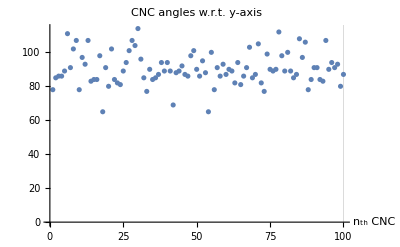
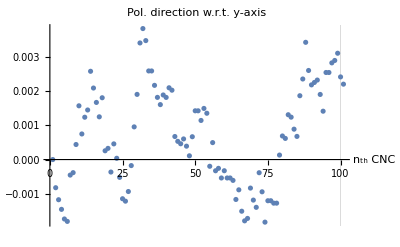
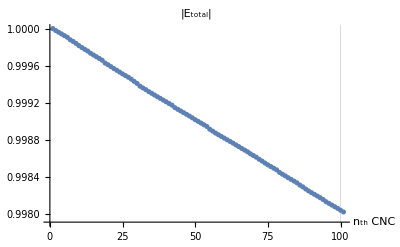
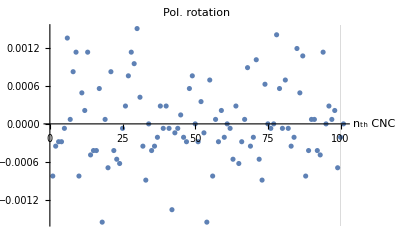

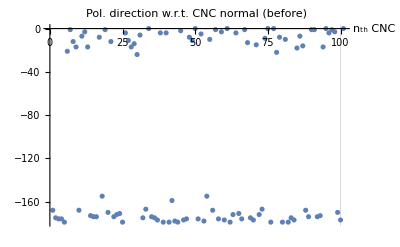
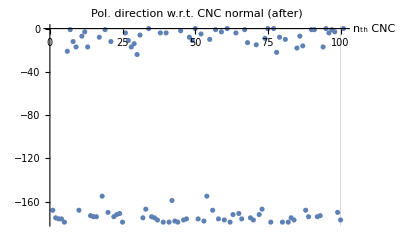

E_total after 100th CNC=0.99802+0. ⅈ

Final intensity after the 2nd polarizer=0.747+0. ⅈ

```mathematica
{ListPlot[ϕun180,ImageSize->400,PlotRange->All,AxesLabel->{"n_th CNC",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},GridLines->{{100},{180}},AxesOrigin->{0,0},PlotLabel->"CNC angles w.r.t. y-axis"],
ListPlot[ψy,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. y-axis",GridLines->{{100},None}],
ListPlot[Etot,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"|E_total|",GridLines->{{100},None}],
ListPlot[(dψ),ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. rotation",GridLines->{{100},None}]}
{ListPlot[ϕbtn,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (before)",GridLines->{{100},None}],
ListPlot[ψres,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (after)",GridLines->{{100},None}]}

Print["E_total after 100th CNC=",Etot[[n+1]]]
Print["Final intensity after the 2nd polarizer=",PI]
```

#### Check numbers after each CNC

```mathematica
AppendTo[ϕun180,0];
AppendTo[ϕun180Norm,0];
ta1=Table[{i,ϕun180[[i]],ψy[[i]],ϕun180Norm[[i]],ϕbtn[[i]],ψres[[i]],dψ[[i]],"",ψy[[i]],dψ2[[i]]," ",Etot[[i]],ttot[[i]]},{i,1,n+1}];
PrependTo[ta1,{"nth CNC","CNC ang(180)","ψy","CNC norm ang","Ang btn(ϕbtn)","ψresult (CNC axis)","dψ(after-before)","+CNC norm","ψy","dψ2(ψ_(n + 1)-ψ_n)","-","E_tot","t_tot"}];
ta1//TableForm
```

nth CNC | CNC ang(180) | ψy | CNC norm ang | Ang btn(ϕbtn) | ψresult (CNC axis) | dψ(after-before) | +CNC norm | ψy | dψ2(ψ_(n + 1)-ψ_n) | - | E_tot | t_tot
1 | 78 | 1.×10^-9 | 168 | -168. | -168.001+0. ⅈ | -0.000821739+0. ⅈ |  | 1.×10^-9 | -0.000821739+0. ⅈ |   | 1 | 0.999979+0. ⅈ
2 | 85 | -0.000821738+0. ⅈ | 175 | -175.001+0. ⅈ | -175.001+0. ⅈ | -0.000350767+0. ⅈ |  | -0.000821738+0. ⅈ | -0.000350767+0. ⅈ |   | 0.999979+0. ⅈ | 0.999981+0. ⅈ
3 | 86 | -0.00117251+0. ⅈ | 176 | -176.001+0. ⅈ | -176.001+0. ⅈ | -0.000281092+0. ⅈ |  | -0.00117251+0. ⅈ | -0.000281092+0. ⅈ |   | 0.99996+0. ⅈ | 0.999982+0. ⅈ
4 | 86 | -0.0014536+0. ⅈ | 176 | -176.001+0. ⅈ | -176.002+0. ⅈ | -0.000281072+0. ⅈ |  | -0.0014536+0. ⅈ | -0.000281072+0. ⅈ |   | 0.999942+0. ⅈ | 0.999982+0. ⅈ
5 | 89 | -0.00173467+0. ⅈ | 179 | -179.002+0. ⅈ | -179.002+0. ⅈ | -0.0000703858+0. ⅈ |  | -0.00173467+0. ⅈ | -0.0000703858+0. ⅈ |   | 0.999924+0. ⅈ | 0.999982+0. ⅈ
6 | 111 | -0.00180506+0. ⅈ | 21 | -21.0018+0. ⅈ | -21.0005+0. ⅈ | 0.00135196+0. ⅈ |  | -0.00180506+0. ⅈ | 0.00135196+0. ⅈ |   | 0.999906+0. ⅈ | 0.999973+0. ⅈ
7 | 91 | -0.000453093+0. ⅈ | 1 | -1.00045+0. ⅈ | -1.00038+0. ⅈ | 0.00007054+0. ⅈ |  | -0.000453093+0. ⅈ | 0.00007054+0. ⅈ |   | 0.999879+0. ⅈ | 0.999982+0. ⅈ
8 | 102 | -0.000382553+0. ⅈ | 12 | -12.0004+0. ⅈ | -11.9996+0. ⅈ | 0.000821764+0. ⅈ |  | -0.000382553+0. ⅈ | 0.000821764+0. ⅈ |   | 0.999861+0. ⅈ | 0.999979+0. ⅈ
9 | 107 | 0.000439211+0. ⅈ | 17 | -16.9996+0. ⅈ | -16.9984+0. ⅈ | 0.00112973+0. ⅈ |  | 0.000439211+0. ⅈ | 0.00112973+0. ⅈ |   | 0.99984+0. ⅈ | 0.999976+0. ⅈ
10 | 78 | 0.00156894+0. ⅈ | 168 | -167.998+0. ⅈ | -167.999+0. ⅈ | -0.000821841+0. ⅈ |  | 0.00156894+0. ⅈ | -0.000821841+0. ⅈ |   | 0.999816+0. ⅈ | 0.999979+0. ⅈ
11 | 97 | 0.000747098+0. ⅈ | 7 | -6.99925+0. ⅈ | -6.99876+0. ⅈ | 0.000488708+0. ⅈ |  | 0.000747098+0. ⅈ | 0.000488708+0. ⅈ |   | 0.999795+0. ⅈ | 0.999981+0. ⅈ
12 | 93 | 0.00123581+0. ⅈ | 3 | -2.99876+0. ⅈ | -2.99855+0. ⅈ | 0.000211094+0. ⅈ |  | 0.00123581+0. ⅈ | 0.000211094+0. ⅈ |   | 0.999776+0. ⅈ | 0.999982+0. ⅈ
13 | 107 | 0.0014469+0. ⅈ | 17 | -16.9986+0. ⅈ | -16.9974+0. ⅈ | 0.00112967+0. ⅈ |  | 0.0014469+0. ⅈ | 0.00112967+0. ⅈ |   | 0.999758+0. ⅈ | 0.999976+0. ⅈ
14 | 83 | 0.00257657+0. ⅈ | 173 | -172.997+0. ⅈ | -172.998+0. ⅈ | -0.000488936+0. ⅈ |  | 0.00257657+0. ⅈ | -0.000488936+0. ⅈ |   | 0.999734+0. ⅈ | 0.999981+0. ⅈ
15 | 84 | 0.00208763+0. ⅈ | 174 | -173.998+0. ⅈ | -173.998+0. ⅈ | -0.000420192+0. ⅈ |  | 0.00208763+0. ⅈ | -0.000420192+0. ⅈ |   | 0.999715+0. ⅈ | 0.999981+0. ⅈ
16 | 84 | 0.00166744+0. ⅈ | 174 | -173.998+0. ⅈ | -173.999+0. ⅈ | -0.000420163+0. ⅈ |  | 0.00166744+0. ⅈ | -0.000420163+0. ⅈ |   | 0.999696+0. ⅈ | 0.999981+0. ⅈ
17 | 98 | 0.00124728+0. ⅈ | 8 | -7.99875+0. ⅈ | -7.9982+0. ⅈ | 0.000556791+0. ⅈ |  | 0.00124728+0. ⅈ | 0.000556791+0. ⅈ |   | 0.999677+0. ⅈ | 0.999981+0. ⅈ
18 | 65 | 0.00180407+0. ⅈ | 155 | -154.998+0. ⅈ | -155.+0. ⅈ | -0.00154775+0. ⅈ |  | 0.00180407+0. ⅈ | -0.00154775+0. ⅈ |   | 0.999658+0. ⅈ | 0.999969+0. ⅈ
19 | 91 | 0.000256316+0. ⅈ | 1 | -0.999744+0. ⅈ | -0.999673+0. ⅈ | 0.00007049+0. ⅈ |  | 0.000256316+0. ⅈ | 0.00007049+0. ⅈ |   | 0.999627+0. ⅈ | 0.999982+0. ⅈ
20 | 80 | 0.000326806+0. ⅈ | 170 | -170.+0. ⅈ | -170.+0. ⅈ | -0.000691012+0. ⅈ |  | 0.000326806+0. ⅈ | -0.000691012+0. ⅈ |   | 0.999609+0. ⅈ | 0.99998+0. ⅈ
21 | 102 | -0.000364206+0. ⅈ | 12 | -12.0004+0. ⅈ | -11.9995+0. ⅈ | 0.000821763+0. ⅈ |  | -0.000364206+0. ⅈ | 0.000821763+0. ⅈ |   | 0.999589+0. ⅈ | 0.999979+0. ⅈ
22 | 84 | 0.000457557+0. ⅈ | 174 | -174.+0. ⅈ | -174.+0. ⅈ | -0.000420079+0. ⅈ |  | 0.000457557+0. ⅈ | -0.000420079+0. ⅈ |   | 0.999568+0. ⅈ | 0.999981+0. ⅈ
23 | 82 | 0.0000374777+0. ⅈ | 172 | -172.+0. ⅈ | -172.001+0. ⅈ | -0.000556878+0. ⅈ |  | 0.0000374777+0. ⅈ | -0.000556878+0. ⅈ |   | 0.999549+0. ⅈ | 0.999981+0. ⅈ
24 | 81 | -0.0005194+0. ⅈ | 171 | -171.001+0. ⅈ | -171.001+0. ⅈ | -0.000624279+0. ⅈ |  | -0.0005194+0. ⅈ | -0.000624279+0. ⅈ |   | 0.99953+0. ⅈ | 0.99998+0. ⅈ
25 | 89 | -0.00114368+0. ⅈ | 179 | -179.001+0. ⅈ | -179.001+0. ⅈ | -0.0000704274+0. ⅈ |  | -0.00114368+0. ⅈ | -0.0000704274+0. ⅈ |   | 0.99951+0. ⅈ | 0.999982+0. ⅈ
26 | 94 | -0.00121411+0. ⅈ | 4 | -4.00121+0. ⅈ | -4.00093+0. ⅈ | 0.000281259+0. ⅈ |  | -0.00121411+0. ⅈ | 0.000281259+0. ⅈ |   | 0.999492+0. ⅈ | 0.999982+0. ⅈ
27 | 101 | -0.000932848+0. ⅈ | 11 | -11.0009+0. ⅈ | -11.0002+0. ⅈ | 0.000756887+0. ⅈ |  | -0.000932848+0. ⅈ | 0.000756887+0. ⅈ |   | 0.999474+0. ⅈ | 0.999979+0. ⅈ
28 | 107 | -0.000175961+0. ⅈ | 17 | -17.0002+0. ⅈ | -16.999+0. ⅈ | 0.00112976+0. ⅈ |  | -0.000175961+0. ⅈ | 0.00112976+0. ⅈ |   | 0.999454+0. ⅈ | 0.999976+0. ⅈ
29 | 104 | 0.000953803+0. ⅈ | 14 | -13.999+0. ⅈ | -13.9981+0. ⅈ | 0.000948426+0. ⅈ |  | 0.000953803+0. ⅈ | 0.000948426+0. ⅈ |   | 0.99943+0. ⅈ | 0.999978+0. ⅈ
30 | 114 | 0.00190223+0. ⅈ | 24 | -23.9981+0. ⅈ | -23.9966+0. ⅈ | 0.00150132+0. ⅈ |  | 0.00190223+0. ⅈ | 0.00150132+0. ⅈ |   | 0.999408+0. ⅈ | 0.99997+0. ⅈ
31 | 96 | 0.00340355+0. ⅈ | 6 | -5.9966+0. ⅈ | -5.99618+0. ⅈ | 0.000419813+0. ⅈ |  | 0.00340355+0. ⅈ | 0.000419813+0. ⅈ |   | 0.999378+0. ⅈ | 0.999981+0. ⅈ
32 | 85 | 0.00382336+0. ⅈ | 175 | -174.996+0. ⅈ | -174.997+0. ⅈ | -0.00035109+0. ⅈ |  | 0.00382336+0. ⅈ | -0.00035109+0. ⅈ |   | 0.999359+0. ⅈ | 0.999981+0. ⅈ
33 | 77 | 0.00347227+0. ⅈ | 167 | -166.997+0. ⅈ | -166.997+0. ⅈ | -0.000885872+0. ⅈ |  | 0.00347227+0. ⅈ | -0.000885872+0. ⅈ |   | 0.999341+0. ⅈ | 0.999978+0. ⅈ
34 | 90 | 0.0025864+0. ⅈ | 0 | 0.0025864+0. ⅈ | 0.00258621+0. ⅈ | -1.82399×10^-7+0. ⅈ |  | 0.0025864+0. ⅈ | -1.82399×10^-7+0. ⅈ |   | 0.999319+0. ⅈ | 0.999982+0. ⅈ
35 | 84 | 0.00258621+0. ⅈ | 174 | -173.997+0. ⅈ | -173.998+0. ⅈ | -0.000420226+0. ⅈ |  | 0.00258621+0. ⅈ | -0.000420226+0. ⅈ |   | 0.999301+0. ⅈ | 0.999981+0. ⅈ
36 | 85 | 0.00216599+0. ⅈ | 175 | -174.998+0. ⅈ | -174.998+0. ⅈ | -0.000350975+0. ⅈ |  | 0.00216599+0. ⅈ | -0.000350975+0. ⅈ |   | 0.999282+0. ⅈ | 0.999981+0. ⅈ
37 | 87 | 0.00181501+0. ⅈ | 177 | -176.998+0. ⅈ | -176.998+0. ⅈ | -0.000211308+0. ⅈ |  | 0.00181501+0. ⅈ | -0.000211308+0. ⅈ |   | 0.999264+0. ⅈ | 0.999982+0. ⅈ
38 | 94 | 0.0016037+0. ⅈ | 4 | -3.9984+0. ⅈ | -3.99812+0. ⅈ | 0.000281062+0. ⅈ |  | 0.0016037+0. ⅈ | 0.000281062+0. ⅈ |   | 0.999246+0. ⅈ | 0.999982+0. ⅈ
39 | 89 | 0.00188477+0. ⅈ | 179 | -178.998+0. ⅈ | -178.998+0. ⅈ | -0.0000706409+0. ⅈ |  | 0.00188477+0. ⅈ | -0.0000706409+0. ⅈ |   | 0.999228+0. ⅈ | 0.999982+0. ⅈ
40 | 94 | 0.00181413+0. ⅈ | 4 | -3.99819+0. ⅈ | -3.9979+0. ⅈ | 0.000281047+0. ⅈ |  | 0.00181413+0. ⅈ | 0.000281047+0. ⅈ |   | 0.99921+0. ⅈ | 0.999982+0. ⅈ
41 | 89 | 0.00209517+0. ⅈ | 179 | -178.998+0. ⅈ | -178.998+0. ⅈ | -0.0000706557+0. ⅈ |  | 0.00209517+0. ⅈ | -0.0000706557+0. ⅈ |   | 0.999191+0. ⅈ | 0.999982+0. ⅈ
42 | 69 | 0.00202452+0. ⅈ | 159 | -158.998+0. ⅈ | -158.999+0. ⅈ | -0.00135197+0. ⅈ |  | 0.00202452+0. ⅈ | -0.00135197+0. ⅈ |   | 0.999173+0. ⅈ | 0.999973+0. ⅈ
43 | 88 | 0.000672543+0. ⅈ | 178 | -177.999+0. ⅈ | -177.999+0. ⅈ | -0.000140978+0. ⅈ |  | 0.000672543+0. ⅈ | -0.000140978+0. ⅈ |   | 0.999146+0. ⅈ | 0.999982+0. ⅈ
44 | 89 | 0.000531565+0. ⅈ | 179 | -178.999+0. ⅈ | -179.+0. ⅈ | -0.0000705455+0. ⅈ |  | 0.000531565+0. ⅈ | -0.0000705455+0. ⅈ |   | 0.999128+0. ⅈ | 0.999982+0. ⅈ
45 | 92 | 0.00046102+0. ⅈ | 2 | -1.99954+0. ⅈ | -1.9994+0. ⅈ | 0.000140898+0. ⅈ |  | 0.00046102+0. ⅈ | 0.000140898+0. ⅈ |   | 0.99911+0. ⅈ | 0.999982+0. ⅈ
46 | 87 | 0.000601917+0. ⅈ | 177 | -176.999+0. ⅈ | -177.+0. ⅈ | -0.000211223+0. ⅈ |  | 0.000601917+0. ⅈ | -0.000211223+0. ⅈ |   | 0.999092+0. ⅈ | 0.999982+0. ⅈ
47 | 86 | 0.000390695+0. ⅈ | 176 | -176.+0. ⅈ | -176.+0. ⅈ | -0.000281201+0. ⅈ |  | 0.000390695+0. ⅈ | -0.000281201+0. ⅈ |   | 0.999074+0. ⅈ | 0.999982+0. ⅈ
48 | 98 | 0.000109493+0. ⅈ | 8 | -7.99989+0. ⅈ | -7.99933+0. ⅈ | 0.000556868+0. ⅈ |  | 0.000109493+0. ⅈ | 0.000556868+0. ⅈ |   | 0.999056+0. ⅈ | 0.999981+0. ⅈ
49 | 101 | 0.000666362+0. ⅈ | 11 | -10.9993+0. ⅈ | -10.9986+0. ⅈ | 0.000756782+0. ⅈ |  | 0.000666362+0. ⅈ | 0.000756782+0. ⅈ |   | 0.999036+0. ⅈ | 0.999979+0. ⅈ
50 | 90 | 0.00142314+0. ⅈ | 0 | 0.00142314+0. ⅈ | 0.00142304+0. ⅈ | -1.00363×10^-7+0. ⅈ |  | 0.00142314+0. ⅈ | -1.00363×10^-7+0. ⅈ |   | 0.999016+0. ⅈ | 0.999982+0. ⅈ
51 | 86 | 0.00142304+0. ⅈ | 176 | -175.999+0. ⅈ | -175.999+0. ⅈ | -0.000281273+0. ⅈ |  | 0.00142304+0. ⅈ | -0.000281273+0. ⅈ |   | 0.998998+0. ⅈ | 0.999982+0. ⅈ
52 | 95 | 0.00114177+0. ⅈ | 5 | -4.99886+0. ⅈ | -4.99851+0. ⅈ | 0.000350745+0. ⅈ |  | 0.00114177+0. ⅈ | 0.000350745+0. ⅈ |   | 0.99898+0. ⅈ | 0.999981+0. ⅈ
53 | 88 | 0.00149252+0. ⅈ | 178 | -177.999+0. ⅈ | -177.999+0. ⅈ | -0.000141035+0. ⅈ |  | 0.00149252+0. ⅈ | -0.000141035+0. ⅈ |   | 0.998961+0. ⅈ | 0.999982+0. ⅈ
54 | 65 | 0.00135148+0. ⅈ | 155 | -154.999+0. ⅈ | -155.+0. ⅈ | -0.00154773+0. ⅈ |  | 0.00135148+0. ⅈ | -0.00154773+0. ⅈ |   | 0.998943+0. ⅈ | 0.999969+0. ⅈ
55 | 100 | -0.000196253+0. ⅈ | 10 | -10.0002+0. ⅈ | -9.99951+0. ⅈ | 0.000691004+0. ⅈ |  | -0.000196253+0. ⅈ | 0.000691004+0. ⅈ |   | 0.998913+0. ⅈ | 0.99998+0. ⅈ
56 | 78 | 0.000494751+0. ⅈ | 168 | -168.+0. ⅈ | -168.+0. ⅈ | -0.000821771+0. ⅈ |  | 0.000494751+0. ⅈ | -0.000821771+0. ⅈ |   | 0.998893+0. ⅈ | 0.999979+0. ⅈ
57 | 91 | -0.000327021+0. ⅈ | 1 | -1.00033+0. ⅈ | -1.00026+0. ⅈ | 0.0000705311+0. ⅈ |  | -0.000327021+0. ⅈ | 0.0000705311+0. ⅈ |   | 0.998872+0. ⅈ | 0.999982+0. ⅈ
58 | 86 | -0.00025649+0. ⅈ | 176 | -176.+0. ⅈ | -176.001+0. ⅈ | -0.000281156+0. ⅈ |  | -0.00025649+0. ⅈ | -0.000281156+0. ⅈ |   | 0.998854+0. ⅈ | 0.999982+0. ⅈ
59 | 93 | -0.000537646+0. ⅈ | 3 | -3.00054+0. ⅈ | -3.00033+0. ⅈ | 0.000211218+0. ⅈ |  | -0.000537646+0. ⅈ | 0.000211218+0. ⅈ |   | 0.998835+0. ⅈ | 0.999982+0. ⅈ
60 | 87 | -0.000326427+0. ⅈ | 177 | -177.+0. ⅈ | -177.001+0. ⅈ | -0.000211158+0. ⅈ |  | -0.000326427+0. ⅈ | -0.000211158+0. ⅈ |   | 0.998817+0. ⅈ | 0.999982+0. ⅈ
61 | 90 | -0.000537585+0. ⅈ | 0 | -0.000537585+0. ⅈ | -0.000537547+0. ⅈ | 3.79118×10^-8+0. ⅈ |  | -0.000537585+0. ⅈ | 3.79118×10^-8+0. ⅈ |   | 0.998799+0. ⅈ | 0.999982+0. ⅈ
62 | 89 | -0.000537547+0. ⅈ | 179 | -179.001+0. ⅈ | -179.001+0. ⅈ | -0.0000704702+0. ⅈ |  | -0.000537547+0. ⅈ | -0.0000704702+0. ⅈ |   | 0.998781+0. ⅈ | 0.999982+0. ⅈ
63 | 82 | -0.000608017+0. ⅈ | 172 | -172.001+0. ⅈ | -172.001+0. ⅈ | -0.000556834+0. ⅈ |  | -0.000608017+0. ⅈ | -0.000556834+0. ⅈ |   | 0.998763+0. ⅈ | 0.999981+0. ⅈ
64 | 94 | -0.00116485+0. ⅈ | 4 | -4.00116+0. ⅈ | -4.00088+0. ⅈ | 0.000281255+0. ⅈ |  | -0.00116485+0. ⅈ | 0.000281255+0. ⅈ |   | 0.998744+0. ⅈ | 0.999982+0. ⅈ
65 | 81 | -0.000883596+0. ⅈ | 171 | -171.001+0. ⅈ | -171.002+0. ⅈ | -0.000624254+0. ⅈ |  | -0.000883596+0. ⅈ | -0.000624254+0. ⅈ |   | 0.998725+0. ⅈ | 0.99998+0. ⅈ
66 | 86 | -0.00150785+0. ⅈ | 176 | -176.002+0. ⅈ | -176.002+0. ⅈ | -0.000281069+0. ⅈ |  | -0.00150785+0. ⅈ | -0.000281069+0. ⅈ |   | 0.998706+0. ⅈ | 0.999982+0. ⅈ
67 | 91 | -0.00178892+0. ⅈ | 1 | -1.00179+0. ⅈ | -1.00172+0. ⅈ | 0.0000706341+0. ⅈ |  | -0.00178892+0. ⅈ | 0.0000706341+0. ⅈ |   | 0.998688+0. ⅈ | 0.999982+0. ⅈ
68 | 103 | -0.00171828+0. ⅈ | 13 | -13.0017+0. ⅈ | -13.0008+0. ⅈ | 0.000885761+0. ⅈ |  | -0.00171828+0. ⅈ | 0.000885761+0. ⅈ |   | 0.99867+0. ⅈ | 0.999978+0. ⅈ
69 | 85 | -0.000832524+0. ⅈ | 175 | -175.001+0. ⅈ | -175.001+0. ⅈ | -0.000350767+0. ⅈ |  | -0.000832524+0. ⅈ | -0.000350767+0. ⅈ |   | 0.998648+0. ⅈ | 0.999981+0. ⅈ
70 | 87 | -0.00118329+0. ⅈ | 177 | -177.001+0. ⅈ | -177.001+0. ⅈ | -0.000211098+0. ⅈ |  | -0.00118329+0. ⅈ | -0.000211098+0. ⅈ |   | 0.99863+0. ⅈ | 0.999982+0. ⅈ
71 | 105 | -0.00139439+0. ⅈ | 15 | -15.0014+0. ⅈ | -15.0004+0. ⅈ | 0.00101025+0. ⅈ |  | -0.00139439+0. ⅈ | 0.00101025+0. ⅈ |   | 0.998611+0. ⅈ | 0.999977+0. ⅈ
72 | 82 | -0.00038414+0. ⅈ | 172 | -172.+0. ⅈ | -172.001+0. ⅈ | -0.00055685+0. ⅈ |  | -0.00038414+0. ⅈ | -0.00055685+0. ⅈ |   | 0.998589+0. ⅈ | 0.999981+0. ⅈ
73 | 77 | -0.00094099+0. ⅈ | 167 | -167.001+0. ⅈ | -167.002+0. ⅈ | -0.000885592+0. ⅈ |  | -0.00094099+0. ⅈ | -0.000885592+0. ⅈ |   | 0.998569+0. ⅈ | 0.999978+0. ⅈ
74 | 99 | -0.00182658+0. ⅈ | 9 | -9.00183+0. ⅈ | -9.0012+0. ⅈ | 0.000624436+0. ⅈ |  | -0.00182658+0. ⅈ | 0.000624436+0. ⅈ |   | 0.998548+0. ⅈ | 0.99998+0. ⅈ
75 | 90 | -0.00120215+0. ⅈ | 0 | -0.00120215+0. ⅈ | -0.00120206+0. ⅈ | 8.47782×10^-8+0. ⅈ |  | -0.00120215+0. ⅈ | 8.47782×10^-8+0. ⅈ |   | 0.998528+0. ⅈ | 0.999982+0. ⅈ
76 | 89 | -0.00120206+0. ⅈ | 179 | -179.001+0. ⅈ | -179.001+0. ⅈ | -0.0000704233+0. ⅈ |  | -0.00120206+0. ⅈ | -0.0000704233+0. ⅈ |   | 0.99851+0. ⅈ | 0.999982+0. ⅈ
77 | 90 | -0.00127248+0. ⅈ | 0 | -0.00127248+0. ⅈ | -0.00127239+0. ⅈ | 8.97386×10^-8+0. ⅈ |  | -0.00127248+0. ⅈ | 8.97386×10^-8+0. ⅈ |   | 0.998492+0. ⅈ | 0.999982+0. ⅈ
78 | 112 | -0.00127239+0. ⅈ | 22 | -22.0013+0. ⅈ | -21.9999+0. ⅈ | 0.00140351+0. ⅈ |  | -0.00127239+0. ⅈ | 0.00140351+0. ⅈ |   | 0.998474+0. ⅈ | 0.999972+0. ⅈ
79 | 98 | 0.000131114+0. ⅈ | 8 | -7.99987+0. ⅈ | -7.99931+0. ⅈ | 0.000556867+0. ⅈ |  | 0.000131114+0. ⅈ | 0.000556867+0. ⅈ |   | 0.998447+0. ⅈ | 0.999981+0. ⅈ
80 | 89 | 0.00068798+0. ⅈ | 179 | -178.999+0. ⅈ | -178.999+0. ⅈ | -0.0000705565+0. ⅈ |  | 0.00068798+0. ⅈ | -0.0000705565+0. ⅈ |   | 0.998427+0. ⅈ | 0.999982+0. ⅈ
81 | 100 | 0.000617424+0. ⅈ | 10 | -9.99938+0. ⅈ | -9.99869+0. ⅈ | 0.00069095+0. ⅈ |  | 0.000617424+0. ⅈ | 0.00069095+0. ⅈ |   | 0.998409+0. ⅈ | 0.99998+0. ⅈ
82 | 89 | 0.00130837+0. ⅈ | 179 | -178.999+0. ⅈ | -178.999+0. ⅈ | -0.0000706003+0. ⅈ |  | 0.00130837+0. ⅈ | -0.0000706003+0. ⅈ |   | 0.998389+0. ⅈ | 0.999982+0. ⅈ
83 | 85 | 0.00123777+0. ⅈ | 175 | -174.999+0. ⅈ | -174.999+0. ⅈ | -0.000350911+0. ⅈ |  | 0.00123777+0. ⅈ | -0.000350911+0. ⅈ |   | 0.998371+0. ⅈ | 0.999981+0. ⅈ
84 | 87 | 0.000886863+0. ⅈ | 177 | -176.999+0. ⅈ | -176.999+0. ⅈ | -0.000211243+0. ⅈ |  | 0.000886863+0. ⅈ | -0.000211243+0. ⅈ |   | 0.998353+0. ⅈ | 0.999982+0. ⅈ
85 | 108 | 0.00067562+0. ⅈ | 18 | -17.9993+0. ⅈ | -17.9981+0. ⅈ | 0.00118748+0. ⅈ |  | 0.00067562+0. ⅈ | 0.00118748+0. ⅈ |   | 0.998335+0. ⅈ | 0.999975+0. ⅈ
86 | 97 | 0.0018631+0. ⅈ | 7 | -6.99814+0. ⅈ | -6.99765+0. ⅈ | 0.000488632+0. ⅈ |  | 0.0018631+0. ⅈ | 0.000488632+0. ⅈ |   | 0.99831+0. ⅈ | 0.999981+0. ⅈ
87 | 106 | 0.00235173+0. ⅈ | 16 | -15.9976+0. ⅈ | -15.9966+0. ⅈ | 0.00107047+0. ⅈ |  | 0.00235173+0. ⅈ | 0.00107047+0. ⅈ |   | 0.998291+0. ⅈ | 0.999977+0. ⅈ
88 | 78 | 0.0034222+0. ⅈ | 168 | -167.997+0. ⅈ | -167.997+0. ⅈ | -0.00082196+0. ⅈ |  | 0.0034222+0. ⅈ | -0.00082196+0. ⅈ |   | 0.998268+0. ⅈ | 0.999979+0. ⅈ
89 | 84 | 0.00260024+0. ⅈ | 174 | -173.997+0. ⅈ | -173.998+0. ⅈ | -0.000420227+0. ⅈ |  | 0.00260024+0. ⅈ | -0.000420227+0. ⅈ |   | 0.998247+0. ⅈ | 0.999981+0. ⅈ
90 | 91 | 0.00218002+0. ⅈ | 1 | -0.99782+0. ⅈ | -0.99775+0. ⅈ | 0.0000703544+0. ⅈ |  | 0.00218002+0. ⅈ | 0.0000703544+0. ⅈ |   | 0.998228+0. ⅈ | 0.999982+0. ⅈ
91 | 91 | 0.00225037+0. ⅈ | 1 | -0.99775+0. ⅈ | -0.997679+0. ⅈ | 0.0000703494+0. ⅈ |  | 0.00225037+0. ⅈ | 0.0000703494+0. ⅈ |   | 0.99821+0. ⅈ | 0.999982+0. ⅈ
92 | 84 | 0.00232072+0. ⅈ | 174 | -173.998+0. ⅈ | -173.998+0. ⅈ | -0.000420208+0. ⅈ |  | 0.00232072+0. ⅈ | -0.000420208+0. ⅈ |   | 0.998192+0. ⅈ | 0.999981+0. ⅈ
93 | 83 | 0.00190051+0. ⅈ | 173 | -172.998+0. ⅈ | -172.999+0. ⅈ | -0.000488889+0. ⅈ |  | 0.00190051+0. ⅈ | -0.000488889+0. ⅈ |   | 0.998173+0. ⅈ | 0.999981+0. ⅈ
94 | 107 | 0.00141162+0. ⅈ | 17 | -16.9986+0. ⅈ | -16.9975+0. ⅈ | 0.00112967+0. ⅈ |  | 0.00141162+0. ⅈ | 0.00112967+0. ⅈ |   | 0.998154+0. ⅈ | 0.999976+0. ⅈ
95 | 90 | 0.00254129+0. ⅈ | 0 | 0.00254129+0. ⅈ | 0.00254112+0. ⅈ | -1.79218×10^-7+0. ⅈ |  | 0.00254129+0. ⅈ | -1.79218×10^-7+0. ⅈ |   | 0.998131+0. ⅈ | 0.999982+0. ⅈ
96 | 94 | 0.00254112+0. ⅈ | 4 | -3.99746+0. ⅈ | -3.99718+0. ⅈ | 0.000280996+0. ⅈ |  | 0.00254112+0. ⅈ | 0.000280996+0. ⅈ |   | 0.998113+0. ⅈ | 0.999982+0. ⅈ
97 | 91 | 0.00282211+0. ⅈ | 1 | -0.997178+0. ⅈ | -0.997108+0. ⅈ | 0.0000703091+0. ⅈ |  | 0.00282211+0. ⅈ | 0.0000703091+0. ⅈ |   | 0.998094+0. ⅈ | 0.999982+0. ⅈ
98 | 93 | 0.00289242+0. ⅈ | 3 | -2.99711+0. ⅈ | -2.9969+0. ⅈ | 0.000210978+0. ⅈ |  | 0.00289242+0. ⅈ | 0.000210978+0. ⅈ |   | 0.998076+0. ⅈ | 0.999982+0. ⅈ
99 | 80 | 0.0031034+0. ⅈ | 170 | -169.997+0. ⅈ | -169.998+0. ⅈ | -0.000691196+0. ⅈ |  | 0.0031034+0. ⅈ | -0.000691196+0. ⅈ |   | 0.998058+0. ⅈ | 0.99998+0. ⅈ
100 | 87 | 0.0024122+0. ⅈ | 177 | -176.998+0. ⅈ | -176.998+0. ⅈ | -0.00021135+0. ⅈ |  | 0.0024122+0. ⅈ | -0.00021135+0. ⅈ |   | 0.998038+0. ⅈ | 0.999982+0. ⅈ
101 | 0 | 0.00220085+0. ⅈ | 0 | 0 | 0 | 0 |  | 0.00220085+0. ⅈ | 0 |   | 0.99802+0. ⅈ | 0

### 5) Bimodal

#### Storage

```mathematica
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

Etot
ϕhe180

ψy
ϕbtn;
ψres;

dψ;
dψ2;
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,0}

{1.×10^-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Loop

```mathematica
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕbi180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕbi180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)
]
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕ1)*π/180])^2; (* I=(|Subscript[E, total]|*sinψ)^2 - Equation 5 *)
```

#### Check plots and final intensity

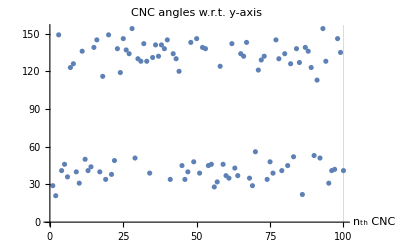
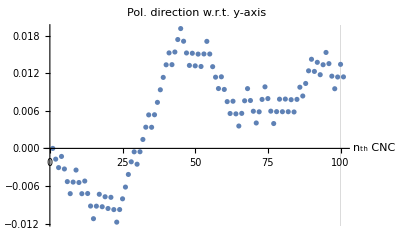
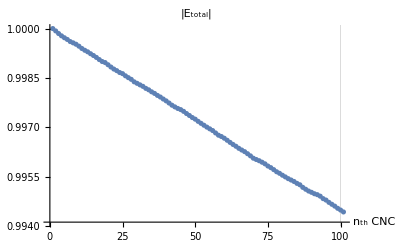
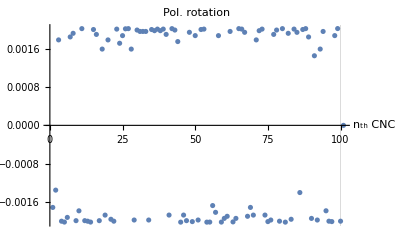

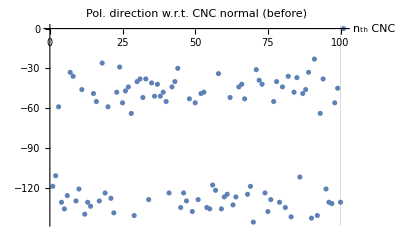
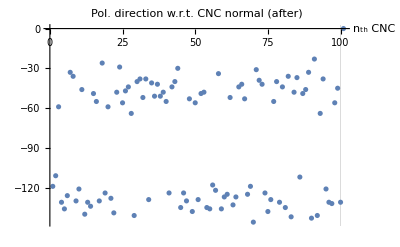

E_total after 100th CNC=0.994422+0. ⅈ

Final intensity after the 2nd polarizer=0.741486+0. ⅈ

```mathematica
{ListPlot[ϕbi180,ImageSize->400,PlotRange->All,AxesLabel->{"n_th CNC",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},GridLines->{{100},{180}},AxesOrigin->{0,0},PlotLabel->"CNC angles w.r.t. y-axis"],
ListPlot[ψy,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. y-axis",GridLines->{{100},None}],
ListPlot[Etot,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"|E_total|",GridLines->{{100},None}],
ListPlot[(dψ),ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. rotation",GridLines->{{100},None}]}
{ListPlot[ϕbtn,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (before)",GridLines->{{100},None}],
ListPlot[ψres,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (after)",GridLines->{{100},None}]}

Print["E_total after 100th CNC=",Etot[[n+1]]]
Print["Final intensity after the 2nd polarizer=",PI]
```

#### Check numbers after each CNC

```mathematica
AppendTo[ϕbi180,0];
AppendTo[ϕbi180Norm,0];
ta1=Table[{i,ϕbi180[[i]],ψy[[i]],ϕbi180Norm[[i]],ϕbtn[[i]],ψres[[i]],dψ[[i]],"",ψy[[i]],dψ2[[i]]," ",Etot[[i]],ttot[[i]]},{i,1,n+1}];
PrependTo[ta1,{"nth CNC","CNC ang(180)","ψy","CNC norm ang","Ang btn(ϕbtn)","ψresult (CNC axis)","dψ(after-before)","+CNC norm","ψy","dψ2(ψ_(n + 1)-ψ_n)","-","E_tot","t_tot"}];
ta1//TableForm
```

nth CNC | CNC ang(180) | ψy | CNC norm ang | Ang btn(ϕbtn) | ψresult (CNC axis) | dψ(after-before) | +CNC norm | ψy | dψ2(ψ_(n + 1)-ψ_n) | - | E_tot | t_tot
1 | 29 | 1.×10^-9 | 119 | -119. | -119.002+0. ⅈ | -0.00171342+0. ⅈ |  | 1.×10^-9 | -0.00171342+0. ⅈ |   | 1 | 0.999928+0. ⅈ
2 | 21 | -0.00171342+0. ⅈ | 111 | -111.002+0. ⅈ | -111.003+0. ⅈ | -0.00135203+0. ⅈ |  | -0.00171342+0. ⅈ | -0.00135203+0. ⅈ |   | 0.999928+0. ⅈ | 0.999921+0. ⅈ
3 | 149 | -0.00306545+0. ⅈ | 59 | -59.0031+0. ⅈ | -59.0013+0. ⅈ | 0.00178383+0. ⅈ |  | -0.00306545+0. ⅈ | 0.00178383+0. ⅈ |   | 0.999849+0. ⅈ | 0.99993+0. ⅈ
4 | 41 | -0.00128162+0. ⅈ | 131 | -131.001+0. ⅈ | -131.003+0. ⅈ | -0.00200075+0. ⅈ |  | -0.00128162+0. ⅈ | -0.00200075+0. ⅈ |   | 0.999779+0. ⅈ | 0.999942+0. ⅈ
5 | 46 | -0.00328237+0. ⅈ | 136 | -136.003+0. ⅈ | -136.005+0. ⅈ | -0.00201915+0. ⅈ |  | -0.00328237+0. ⅈ | -0.00201915+0. ⅈ |   | 0.999721+0. ⅈ | 0.999948+0. ⅈ
6 | 36 | -0.00530152+0. ⅈ | 126 | -126.005+0. ⅈ | -126.007+0. ⅈ | -0.00192164+0. ⅈ |  | -0.00530152+0. ⅈ | -0.00192164+0. ⅈ |   | 0.999669+0. ⅈ | 0.999936+0. ⅈ
7 | 123 | -0.00722316+0. ⅈ | 33 | -33.0072+0. ⅈ | -33.0054+0. ⅈ | 0.0018459+0. ⅈ |  | -0.00722316+0. ⅈ | 0.0018459+0. ⅈ |   | 0.999605+0. ⅈ | 0.999961+0. ⅈ
8 | 126 | -0.00537726+0. ⅈ | 36 | -36.0054+0. ⅈ | -36.0035+0. ⅈ | 0.0019216+0. ⅈ |  | -0.00537726+0. ⅈ | 0.0019216+0. ⅈ |   | 0.999566+0. ⅈ | 0.999958+0. ⅈ
9 | 40 | -0.00345566+0. ⅈ | 130 | -130.003+0. ⅈ | -130.005+0. ⅈ | -0.00198975+0. ⅈ |  | -0.00345566+0. ⅈ | -0.00198975+0. ⅈ |   | 0.999523+0. ⅈ | 0.999941+0. ⅈ
10 | 31 | -0.00544541+0. ⅈ | 121 | -121.005+0. ⅈ | -121.007+0. ⅈ | -0.00178411+0. ⅈ |  | -0.00544541+0. ⅈ | -0.00178411+0. ⅈ |   | 0.999464+0. ⅈ | 0.99993+0. ⅈ
11 | 136 | -0.00722952+0. ⅈ | 46 | -46.0072+0. ⅈ | -46.0052+0. ⅈ | 0.00201914+0. ⅈ |  | -0.00722952+0. ⅈ | 0.00201914+0. ⅈ |   | 0.999394+0. ⅈ | 0.999946+0. ⅈ
12 | 50 | -0.00521037+0. ⅈ | 140 | -140.005+0. ⅈ | -140.007+0. ⅈ | -0.00198962+0. ⅈ |  | -0.00521037+0. ⅈ | -0.00198962+0. ⅈ |   | 0.99934+0. ⅈ | 0.999953+0. ⅈ
13 | 41 | -0.00719999+0. ⅈ | 131 | -131.007+0. ⅈ | -131.009+0. ⅈ | -0.00200081+0. ⅈ |  | -0.00719999+0. ⅈ | -0.00200081+0. ⅈ |   | 0.999293+0. ⅈ | 0.999942+0. ⅈ
14 | 44 | -0.0092008+0. ⅈ | 134 | -134.009+0. ⅈ | -134.011+0. ⅈ | -0.00201918+0. ⅈ |  | -0.0092008+0. ⅈ | -0.00201918+0. ⅈ |   | 0.999235+0. ⅈ | 0.999946+0. ⅈ
15 | 139 | -0.01122+0. ⅈ | 49 | -49.0112+0. ⅈ | -49.0092+0. ⅈ | 0.00200063+0. ⅈ |  | -0.01122+0. ⅈ | 0.00200063+0. ⅈ |   | 0.99918+0. ⅈ | 0.999942+0. ⅈ
16 | 145 | -0.00921935+0. ⅈ | 55 | -55.0092+0. ⅈ | -55.0073+0. ⅈ | 0.00189834+0. ⅈ |  | -0.00921935+0. ⅈ | 0.00189834+0. ⅈ |   | 0.999122+0. ⅈ | 0.999935+0. ⅈ
17 | 40 | -0.00732101+0. ⅈ | 130 | -130.007+0. ⅈ | -130.009+0. ⅈ | -0.0019898+0. ⅈ |  | -0.00732101+0. ⅈ | -0.0019898+0. ⅈ |   | 0.999057+0. ⅈ | 0.999941+0. ⅈ
18 | 116 | -0.00931081+0. ⅈ | 26 | -26.0093+0. ⅈ | -26.0077+0. ⅈ | 0.00159246+0. ⅈ |  | -0.00931081+0. ⅈ | 0.00159246+0. ⅈ |   | 0.998998+0. ⅈ | 0.999968+0. ⅈ
19 | 34 | -0.00771835+0. ⅈ | 124 | -124.008+0. ⅈ | -124.01+0. ⅈ | -0.0018735+0. ⅈ |  | -0.00771835+0. ⅈ | -0.0018735+0. ⅈ |   | 0.998966+0. ⅈ | 0.999934+0. ⅈ
20 | 149 | -0.00959185+0. ⅈ | 59 | -59.0096+0. ⅈ | -59.0078+0. ⅈ | 0.00178361+0. ⅈ |  | -0.00959185+0. ⅈ | 0.00178361+0. ⅈ |   | 0.9989+0. ⅈ | 0.99993+0. ⅈ
21 | 38 | -0.00780824+0. ⅈ | 128 | -128.008+0. ⅈ | -128.01+0. ⅈ | -0.00196052+0. ⅈ |  | -0.00780824+0. ⅈ | -0.00196052+0. ⅈ |   | 0.99883+0. ⅈ | 0.999938+0. ⅈ
22 | 49 | -0.00976876+0. ⅈ | 139 | -139.01+0. ⅈ | -139.012+0. ⅈ | -0.00200062+0. ⅈ |  | -0.00976876+0. ⅈ | -0.00200062+0. ⅈ |   | 0.998769+0. ⅈ | 0.999952+0. ⅈ
23 | 138 | -0.0117694+0. ⅈ | 48 | -48.0118+0. ⅈ | -48.0098+0. ⅈ | 0.00200924+0. ⅈ |  | -0.0117694+0. ⅈ | 0.00200924+0. ⅈ |   | 0.99872+0. ⅈ | 0.999943+0. ⅈ
24 | 119 | -0.00976014+0. ⅈ | 29 | -29.0098+0. ⅈ | -29.008+0. ⅈ | 0.00171372+0. ⅈ |  | -0.00976014+0. ⅈ | 0.00171372+0. ⅈ |   | 0.998663+0. ⅈ | 0.999965+0. ⅈ
25 | 146 | -0.00804642+0. ⅈ | 56 | -56.008+0. ⅈ | -56.0062+0. ⅈ | 0.00187308+0. ⅈ |  | -0.00804642+0. ⅈ | 0.00187308+0. ⅈ |   | 0.998629+0. ⅈ | 0.999934+0. ⅈ
26 | 137 | -0.00617334+0. ⅈ | 47 | -47.0062+0. ⅈ | -47.0042+0. ⅈ | 0.00201544+0. ⅈ |  | -0.00617334+0. ⅈ | 0.00201544+0. ⅈ |   | 0.998563+0. ⅈ | 0.999944+0. ⅈ
27 | 134 | -0.0041579+0. ⅈ | 44 | -44.0042+0. ⅈ | -44.0021+0. ⅈ | 0.00201917+0. ⅈ |  | -0.0041579+0. ⅈ | 0.00201917+0. ⅈ |   | 0.998507+0. ⅈ | 0.999948+0. ⅈ
28 | 154 | -0.00213873+0. ⅈ | 64 | -64.0021+0. ⅈ | -64.0005+0. ⅈ | 0.00159203+0. ⅈ |  | -0.00213873+0. ⅈ | 0.00159203+0. ⅈ |   | 0.998455+0. ⅈ | 0.999925+0. ⅈ
29 | 51 | -0.000546704+0. ⅈ | 141 | -141.001+0. ⅈ | -141.003+0. ⅈ | -0.00197622+0. ⅈ |  | -0.000546704+0. ⅈ | -0.00197622+0. ⅈ |   | 0.99838+0. ⅈ | 0.999954+0. ⅈ
30 | 130 | -0.00252292+0. ⅈ | 40 | -40.0025+0. ⅈ | -40.0005+0. ⅈ | 0.00198971+0. ⅈ |  | -0.00252292+0. ⅈ | 0.00198971+0. ⅈ |   | 0.998334+0. ⅈ | 0.999953+0. ⅈ
31 | 128 | -0.000533207+0. ⅈ | 38 | -38.0005+0. ⅈ | -37.9986+0. ⅈ | 0.00196037+0. ⅈ |  | -0.000533207+0. ⅈ | 0.00196037+0. ⅈ |   | 0.998287+0. ⅈ | 0.999955+0. ⅈ
32 | 142 | 0.00142716+0. ⅈ | 52 | -51.9986+0. ⅈ | -51.9966+0. ⅈ | 0.00196042+0. ⅈ |  | 0.00142716+0. ⅈ | 0.00196042+0. ⅈ |   | 0.998243+0. ⅈ | 0.999938+0. ⅈ
33 | 128 | 0.00338757+0. ⅈ | 38 | -37.9966+0. ⅈ | -37.9947+0. ⅈ | 0.0019603+0. ⅈ |  | 0.00338757+0. ⅈ | 0.0019603+0. ⅈ |   | 0.998181+0. ⅈ | 0.999955+0. ⅈ
34 | 39 | 0.00534787+0. ⅈ | 129 | -128.995+0. ⅈ | -128.997+0. ⅈ | -0.00197617+0. ⅈ |  | 0.00534787+0. ⅈ | -0.00197617+0. ⅈ |   | 0.998136+0. ⅈ | 0.999939+0. ⅈ
35 | 131 | 0.0033717+0. ⅈ | 41 | -40.9966+0. ⅈ | -40.9946+0. ⅈ | 0.00200068+0. ⅈ |  | 0.0033717+0. ⅈ | 0.00200068+0. ⅈ |   | 0.998076+0. ⅈ | 0.999952+0. ⅈ
36 | 141 | 0.00537238+0. ⅈ | 51 | -50.9946+0. ⅈ | -50.9927+0. ⅈ | 0.00197633+0. ⅈ |  | 0.00537238+0. ⅈ | 0.00197633+0. ⅈ |   | 0.998028+0. ⅈ | 0.999939+0. ⅈ
37 | 132 | 0.00734871+0. ⅈ | 42 | -41.9927+0. ⅈ | -41.9906+0. ⅈ | 0.00200926+0. ⅈ |  | 0.00734871+0. ⅈ | 0.00200926+0. ⅈ |   | 0.997967+0. ⅈ | 0.99995+0. ⅈ
38 | 141 | 0.00935797+0. ⅈ | 51 | -50.9906+0. ⅈ | -50.9887+0. ⅈ | 0.00197639+0. ⅈ |  | 0.00935797+0. ⅈ | 0.00197639+0. ⅈ |   | 0.997918+0. ⅈ | 0.999939+0. ⅈ
39 | 138 | 0.0113344+0. ⅈ | 48 | -47.9887+0. ⅈ | -47.9867+0. ⅈ | 0.00200941+0. ⅈ |  | 0.0113344+0. ⅈ | 0.00200941+0. ⅈ |   | 0.997857+0. ⅈ | 0.999943+0. ⅈ
40 | 145 | 0.0133438+0. ⅈ | 55 | -54.9867+0. ⅈ | -54.9848+0. ⅈ | 0.00189889+0. ⅈ |  | 0.0133438+0. ⅈ | 0.00189889+0. ⅈ |   | 0.997801+0. ⅈ | 0.999935+0. ⅈ
41 | 34 | 0.0152427+0. ⅈ | 124 | -123.985+0. ⅈ | -123.987+0. ⅈ | -0.00187289+0. ⅈ |  | 0.0152427+0. ⅈ | -0.00187289+0. ⅈ |   | 0.997736+0. ⅈ | 0.999934+0. ⅈ
42 | 134 | 0.0133698+0. ⅈ | 44 | -43.9866+0. ⅈ | -43.9846+0. ⅈ | 0.00201912+0. ⅈ |  | 0.0133698+0. ⅈ | 0.00201912+0. ⅈ |   | 0.997669+0. ⅈ | 0.999948+0. ⅈ
43 | 130 | 0.0153889+0. ⅈ | 40 | -39.9846+0. ⅈ | -39.9826+0. ⅈ | 0.00198949+0. ⅈ |  | 0.0153889+0. ⅈ | 0.00198949+0. ⅈ |   | 0.997617+0. ⅈ | 0.999953+0. ⅈ
44 | 120 | 0.0173784+0. ⅈ | 30 | -29.9826+0. ⅈ | -29.9809+0. ⅈ | 0.00174906+0. ⅈ |  | 0.0173784+0. ⅈ | 0.00174906+0. ⅈ |   | 0.99757+0. ⅈ | 0.999964+0. ⅈ
45 | 45 | 0.0191274+0. ⅈ | 135 | -134.981+0. ⅈ | -134.983+0. ⅈ | -0.00202039+0. ⅈ |  | 0.0191274+0. ⅈ | -0.00202039+0. ⅈ |   | 0.997535+0. ⅈ | 0.999947+0. ⅈ
46 | 34 | 0.0171071+0. ⅈ | 124 | -123.983+0. ⅈ | -123.985+0. ⅈ | -0.00187284+0. ⅈ |  | 0.0171071+0. ⅈ | -0.00187284+0. ⅈ |   | 0.997482+0. ⅈ | 0.999934+0. ⅈ
47 | 40 | 0.0152342+0. ⅈ | 130 | -129.985+0. ⅈ | -129.987+0. ⅈ | -0.00198952+0. ⅈ |  | 0.0152342+0. ⅈ | -0.00198952+0. ⅈ |   | 0.997415+0. ⅈ | 0.999941+0. ⅈ
48 | 143 | 0.0132447+0. ⅈ | 53 | -52.9868+0. ⅈ | -52.9848+0. ⅈ | 0.0019424+0. ⅈ |  | 0.0132447+0. ⅈ | 0.0019424+0. ⅈ |   | 0.997356+0. ⅈ | 0.999937+0. ⅈ
49 | 48 | 0.0151871+0. ⅈ | 138 | -137.985+0. ⅈ | -137.987+0. ⅈ | -0.00200942+0. ⅈ |  | 0.0151871+0. ⅈ | -0.00200942+0. ⅈ |   | 0.997293+0. ⅈ | 0.99995+0. ⅈ
50 | 146 | 0.0131777+0. ⅈ | 56 | -55.9868+0. ⅈ | -55.9849+0. ⅈ | 0.00187364+0. ⅈ |  | 0.0131777+0. ⅈ | 0.00187364+0. ⅈ |   | 0.997244+0. ⅈ | 0.999934+0. ⅈ
51 | 39 | 0.0150513+0. ⅈ | 129 | -128.985+0. ⅈ | -128.987+0. ⅈ | -0.00197603+0. ⅈ |  | 0.0150513+0. ⅈ | -0.00197603+0. ⅈ |   | 0.997178+0. ⅈ | 0.999939+0. ⅈ
52 | 139 | 0.0130753+0. ⅈ | 49 | -48.9869+0. ⅈ | -48.9849+0. ⅈ | 0.00200086+0. ⅈ |  | 0.0130753+0. ⅈ | 0.00200086+0. ⅈ |   | 0.997117+0. ⅈ | 0.999942+0. ⅈ
53 | 138 | 0.0150761+0. ⅈ | 48 | -47.9849+0. ⅈ | -47.9829+0. ⅈ | 0.00200944+0. ⅈ |  | 0.0150761+0. ⅈ | 0.00200944+0. ⅈ |   | 0.997059+0. ⅈ | 0.999943+0. ⅈ
54 | 45 | 0.0170856+0. ⅈ | 135 | -134.983+0. ⅈ | -134.985+0. ⅈ | -0.00202039+0. ⅈ |  | 0.0170856+0. ⅈ | -0.00202039+0. ⅈ |   | 0.997003+0. ⅈ | 0.999947+0. ⅈ
55 | 46 | 0.0150652+0. ⅈ | 136 | -135.985+0. ⅈ | -135.987+0. ⅈ | -0.00201919+0. ⅈ |  | 0.0150652+0. ⅈ | -0.00201919+0. ⅈ |   | 0.99695+0. ⅈ | 0.999948+0. ⅈ
56 | 28 | 0.013046+0. ⅈ | 118 | -117.987+0. ⅈ | -117.989+0. ⅈ | -0.0016745+0. ⅈ |  | 0.013046+0. ⅈ | -0.0016745+0. ⅈ |   | 0.996898+0. ⅈ | 0.999927+0. ⅈ
57 | 32 | 0.0113715+0. ⅈ | 122 | -121.989+0. ⅈ | -121.99+0. ⅈ | -0.00181559+0. ⅈ |  | 0.0113715+0. ⅈ | -0.00181559+0. ⅈ |   | 0.996825+0. ⅈ | 0.999931+0. ⅈ
58 | 124 | 0.00955592+0. ⅈ | 34 | -33.9904+0. ⅈ | -33.9886+0. ⅈ | 0.00187299+0. ⅈ |  | 0.00955592+0. ⅈ | 0.00187299+0. ⅈ |   | 0.996757+0. ⅈ | 0.99996+0. ⅈ
59 | 46 | 0.0114289+0. ⅈ | 136 | -135.989+0. ⅈ | -135.991+0. ⅈ | -0.00201918+0. ⅈ |  | 0.0114289+0. ⅈ | -0.00201918+0. ⅈ |   | 0.996717+0. ⅈ | 0.999948+0. ⅈ
60 | 37 | 0.00940973+0. ⅈ | 127 | -126.991+0. ⅈ | -126.993+0. ⅈ | -0.00194196+0. ⅈ |  | 0.00940973+0. ⅈ | -0.00194196+0. ⅈ |   | 0.996665+0. ⅈ | 0.999937+0. ⅈ
61 | 35 | 0.00746777+0. ⅈ | 125 | -124.993+0. ⅈ | -124.994+0. ⅈ | -0.00189839+0. ⅈ |  | 0.00746777+0. ⅈ | -0.00189839+0. ⅈ |   | 0.996602+0. ⅈ | 0.999935+0. ⅈ
62 | 142 | 0.00556939+0. ⅈ | 52 | -51.9944+0. ⅈ | -51.9925+0. ⅈ | 0.00196049+0. ⅈ |  | 0.00556939+0. ⅈ | 0.00196049+0. ⅈ |   | 0.996537+0. ⅈ | 0.999938+0. ⅈ
63 | 43 | 0.00752987+0. ⅈ | 133 | -132.992+0. ⅈ | -132.994+0. ⅈ | -0.00201543+0. ⅈ |  | 0.00752987+0. ⅈ | -0.00201543+0. ⅈ |   | 0.996475+0. ⅈ | 0.999944+0. ⅈ
64 | 37 | 0.00551444+0. ⅈ | 127 | -126.994+0. ⅈ | -126.996+0. ⅈ | -0.00194203+0. ⅈ |  | 0.00551444+0. ⅈ | -0.00194203+0. ⅈ |   | 0.99642+0. ⅈ | 0.999937+0. ⅈ
65 | 134 | 0.0035724+0. ⅈ | 44 | -43.9964+0. ⅈ | -43.9944+0. ⅈ | 0.00201915+0. ⅈ |  | 0.0035724+0. ⅈ | 0.00201915+0. ⅈ |   | 0.996357+0. ⅈ | 0.999948+0. ⅈ
66 | 132 | 0.00559155+0. ⅈ | 42 | -41.9944+0. ⅈ | -41.9924+0. ⅈ | 0.00200927+0. ⅈ |  | 0.00559155+0. ⅈ | 0.00200927+0. ⅈ |   | 0.996305+0. ⅈ | 0.99995+0. ⅈ
67 | 143 | 0.00760082+0. ⅈ | 53 | -52.9924+0. ⅈ | -52.9905+0. ⅈ | 0.00194229+0. ⅈ |  | 0.00760082+0. ⅈ | 0.00194229+0. ⅈ |   | 0.996256+0. ⅈ | 0.999937+0. ⅈ
68 | 35 | 0.00954311+0. ⅈ | 125 | -124.99+0. ⅈ | -124.992+0. ⅈ | -0.00189834+0. ⅈ |  | 0.00954311+0. ⅈ | -0.00189834+0. ⅈ |   | 0.996193+0. ⅈ | 0.999935+0. ⅈ
69 | 29 | 0.00764477+0. ⅈ | 119 | -118.992+0. ⅈ | -118.994+0. ⅈ | -0.00171313+0. ⅈ |  | 0.00764477+0. ⅈ | -0.00171313+0. ⅈ |   | 0.996128+0. ⅈ | 0.999928+0. ⅈ
70 | 56 | 0.00593164+0. ⅈ | 146 | -145.994+0. ⅈ | -145.996+0. ⅈ | -0.0018734+0. ⅈ |  | 0.00593164+0. ⅈ | -0.0018734+0. ⅈ |   | 0.996057+0. ⅈ | 0.99996+0. ⅈ
71 | 121 | 0.00405824+0. ⅈ | 31 | -30.9959+0. ⅈ | -30.9942+0. ⅈ | 0.00178373+0. ⅈ |  | 0.00405824+0. ⅈ | 0.00178373+0. ⅈ |   | 0.996017+0. ⅈ | 0.999963+0. ⅈ
72 | 129 | 0.00584197+0. ⅈ | 39 | -38.9942+0. ⅈ | -38.9922+0. ⅈ | 0.00197614+0. ⅈ |  | 0.00584197+0. ⅈ | 0.00197614+0. ⅈ |   | 0.99598+0. ⅈ | 0.999954+0. ⅈ
73 | 132 | 0.00781811+0. ⅈ | 42 | -41.9922+0. ⅈ | -41.9902+0. ⅈ | 0.00200926+0. ⅈ |  | 0.00781811+0. ⅈ | 0.00200926+0. ⅈ |   | 0.995935+0. ⅈ | 0.99995+0. ⅈ
74 | 34 | 0.00982736+0. ⅈ | 124 | -123.99+0. ⅈ | -123.992+0. ⅈ | -0.00187304+0. ⅈ |  | 0.00982736+0. ⅈ | -0.00187304+0. ⅈ |   | 0.995885+0. ⅈ | 0.999934+0. ⅈ
75 | 48 | 0.00795433+0. ⅈ | 138 | -137.992+0. ⅈ | -137.994+0. ⅈ | -0.00200937+0. ⅈ |  | 0.00795433+0. ⅈ | -0.00200937+0. ⅈ |   | 0.995819+0. ⅈ | 0.99995+0. ⅈ
76 | 39 | 0.00594496+0. ⅈ | 129 | -128.994+0. ⅈ | -128.996+0. ⅈ | -0.00197617+0. ⅈ |  | 0.00594496+0. ⅈ | -0.00197617+0. ⅈ |   | 0.99577+0. ⅈ | 0.999939+0. ⅈ
77 | 145 | 0.00396879+0. ⅈ | 55 | -54.996+0. ⅈ | -54.9941+0. ⅈ | 0.00189866+0. ⅈ |  | 0.00396879+0. ⅈ | 0.00189866+0. ⅈ |   | 0.995709+0. ⅈ | 0.999935+0. ⅈ
78 | 130 | 0.00586745+0. ⅈ | 40 | -39.9941+0. ⅈ | -39.9921+0. ⅈ | 0.00198961+0. ⅈ |  | 0.00586745+0. ⅈ | 0.00198961+0. ⅈ |   | 0.995644+0. ⅈ | 0.999953+0. ⅈ
79 | 41 | 0.00785706+0. ⅈ | 131 | -130.992+0. ⅈ | -130.994+0. ⅈ | -0.00200066+0. ⅈ |  | 0.00785706+0. ⅈ | -0.00200066+0. ⅈ |   | 0.995597+0. ⅈ | 0.999942+0. ⅈ
80 | 134 | 0.0058564+0. ⅈ | 44 | -43.9941+0. ⅈ | -43.9921+0. ⅈ | 0.00201914+0. ⅈ |  | 0.0058564+0. ⅈ | 0.00201914+0. ⅈ |   | 0.99554+0. ⅈ | 0.999948+0. ⅈ
81 | 45 | 0.00787555+0. ⅈ | 135 | -134.992+0. ⅈ | -134.994+0. ⅈ | -0.00202039+0. ⅈ |  | 0.00787555+0. ⅈ | -0.00202039+0. ⅈ |   | 0.995488+0. ⅈ | 0.999947+0. ⅈ
82 | 126 | 0.00585516+0. ⅈ | 36 | -35.9941+0. ⅈ | -35.9922+0. ⅈ | 0.00192135+0. ⅈ |  | 0.00585516+0. ⅈ | 0.00192135+0. ⅈ |   | 0.995435+0. ⅈ | 0.999958+0. ⅈ
83 | 52 | 0.00777651+0. ⅈ | 142 | -141.992+0. ⅈ | -141.994+0. ⅈ | -0.00196049+0. ⅈ |  | 0.00777651+0. ⅈ | -0.00196049+0. ⅈ |   | 0.995393+0. ⅈ | 0.999955+0. ⅈ
84 | 138 | 0.00581602+0. ⅈ | 48 | -47.9942+0. ⅈ | -47.9922+0. ⅈ | 0.00200937+0. ⅈ |  | 0.00581602+0. ⅈ | 0.00200937+0. ⅈ |   | 0.995348+0. ⅈ | 0.999943+0. ⅈ
85 | 127 | 0.00782539+0. ⅈ | 37 | -36.9922+0. ⅈ | -36.9902+0. ⅈ | 0.00194195+0. ⅈ |  | 0.00782539+0. ⅈ | 0.00194195+0. ⅈ |   | 0.995292+0. ⅈ | 0.999956+0. ⅈ
86 | 22 | 0.00976734+0. ⅈ | 112 | -111.99+0. ⅈ | -111.992+0. ⅈ | -0.00140302+0. ⅈ |  | 0.00976734+0. ⅈ | -0.00140302+0. ⅈ |   | 0.995248+0. ⅈ | 0.999921+0. ⅈ
87 | 139 | 0.00836432+0. ⅈ | 49 | -48.9916+0. ⅈ | -48.9896+0. ⅈ | 0.00200082+0. ⅈ |  | 0.00836432+0. ⅈ | 0.00200082+0. ⅈ |   | 0.99517+0. ⅈ | 0.999942+0. ⅈ
88 | 136 | 0.0103651+0. ⅈ | 46 | -45.9896+0. ⅈ | -45.9876+0. ⅈ | 0.00201919+0. ⅈ |  | 0.0103651+0. ⅈ | 0.00201919+0. ⅈ |   | 0.995112+0. ⅈ | 0.999946+0. ⅈ
89 | 123 | 0.0123843+0. ⅈ | 33 | -32.9876+0. ⅈ | -32.9858+0. ⅈ | 0.00184533+0. ⅈ |  | 0.0123843+0. ⅈ | 0.00184533+0. ⅈ |   | 0.995058+0. ⅈ | 0.999961+0. ⅈ
90 | 53 | 0.0142297+0. ⅈ | 143 | -142.986+0. ⅈ | -142.988+0. ⅈ | -0.00194238+0. ⅈ |  | 0.0142297+0. ⅈ | -0.00194238+0. ⅈ |   | 0.995019+0. ⅈ | 0.999956+0. ⅈ
91 | 113 | 0.0122873+0. ⅈ | 23 | -22.9877+0. ⅈ | -22.9863+0. ⅈ | 0.00145271+0. ⅈ |  | 0.0122873+0. ⅈ | 0.00145271+0. ⅈ |   | 0.994976+0. ⅈ | 0.999971+0. ⅈ
92 | 51 | 0.01374+0. ⅈ | 141 | -140.986+0. ⅈ | -140.988+0. ⅈ | -0.00197642+0. ⅈ |  | 0.01374+0. ⅈ | -0.00197642+0. ⅈ |   | 0.994947+0. ⅈ | 0.999954+0. ⅈ
93 | 154 | 0.0117636+0. ⅈ | 64 | -63.9882+0. ⅈ | -63.9866+0. ⅈ | 0.00159263+0. ⅈ |  | 0.0117636+0. ⅈ | 0.00159263+0. ⅈ |   | 0.994902+0. ⅈ | 0.999925+0. ⅈ
94 | 128 | 0.0133562+0. ⅈ | 38 | -37.9866+0. ⅈ | -37.9847+0. ⅈ | 0.00196013+0. ⅈ |  | 0.0133562+0. ⅈ | 0.00196013+0. ⅈ |   | 0.994827+0. ⅈ | 0.999955+0. ⅈ
95 | 31 | 0.0153163+0. ⅈ | 121 | -120.985+0. ⅈ | -120.986+0. ⅈ | -0.00178342+0. ⅈ |  | 0.0153163+0. ⅈ | -0.00178342+0. ⅈ |   | 0.994783+0. ⅈ | 0.99993+0. ⅈ
96 | 41 | 0.0135329+0. ⅈ | 131 | -130.986+0. ⅈ | -130.988+0. ⅈ | -0.0020006+0. ⅈ |  | 0.0135329+0. ⅈ | -0.0020006+0. ⅈ |   | 0.994713+0. ⅈ | 0.999942+0. ⅈ
97 | 42 | 0.0115323+0. ⅈ | 132 | -131.988+0. ⅈ | -131.99+0. ⅈ | -0.00200924+0. ⅈ |  | 0.0115323+0. ⅈ | -0.00200924+0. ⅈ |   | 0.994655+0. ⅈ | 0.999943+0. ⅈ
98 | 146 | 0.00952306+0. ⅈ | 56 | -55.9905+0. ⅈ | -55.9886+0. ⅈ | 0.00187355+0. ⅈ |  | 0.00952306+0. ⅈ | 0.00187355+0. ⅈ |   | 0.994599+0. ⅈ | 0.999934+0. ⅈ
99 | 135 | 0.0113966+0. ⅈ | 45 | -44.9886+0. ⅈ | -44.9866+0. ⅈ | 0.00202039+0. ⅈ |  | 0.0113966+0. ⅈ | 0.00202039+0. ⅈ |   | 0.994533+0. ⅈ | 0.999947+0. ⅈ
100 | 41 | 0.013417+0. ⅈ | 131 | -130.987+0. ⅈ | -130.989+0. ⅈ | -0.0020006+0. ⅈ |  | 0.013417+0. ⅈ | -0.0020006+0. ⅈ |   | 0.99448+0. ⅈ | 0.999942+0. ⅈ
101 | 0 | 0.0114164+0. ⅈ | 0 | 0 | 0 | 0 |  | 0.0114164+0. ⅈ | 0 |   | 0.994422+0. ⅈ | 0

## G. Final intensity as a function of the incident polarization angle Note: the same calculation with various incident polarization angle (no explanation included). Data exportation included.

```mathematica
(*Crossed-polylamellate*)
PIcl[x_]:=Module[{},
ϕi=x+ϵ;(* Polarization direction w.r.t. y-axis *)
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

(**)
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕcl180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕcl180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)

];
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕi)*π/180])^2
]
clAng=Table[{i,PIcl[i]},{i,0,180,5}];
```

```mathematica
(*Random*)
PIra[x_]:=Module[{},
ϕi=x+ϵ;(* Polarization direction w.r.t. y-axis *)
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

(**)
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕra180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕra180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)

];
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕi)*π/180])^2
]
raAng=Table[{i,PIra[i]},{i,0,180,5}];
```

```mathematica
(*Helicoidal*)
PIhe[x_]:=Module[{},
ϕi=x+ϵ;(* Polarization direction w.r.t. y-axis *)
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

(**)
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕhe180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕhe180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)

];
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕi)*π/180])^2
]
heAng=Table[{i,PIhe[i]},{i,0,180,5}];
```

```mathematica
(*Uniaxial*)
PIun[x_]:=Module[{},
ϕi=x+ϵ;(* Polarization direction w.r.t. y-axis *)
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

(**)
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕun180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕun180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)

];
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕi)*π/180])^2
]
unAng=Table[{i,PIun[i]},{i,0,180,5}];
```

```mathematica
(*Bimodal*)
PIbi[x_]:=Module[{},
ϕi=x+ϵ;(* Polarization direction w.r.t. y-axis *)
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

(**)
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕbi180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕbi180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)

];
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕi)*π/180])^2
]
biAng=Table[{i,PIbi[i]},{i,0,180,5}];
```

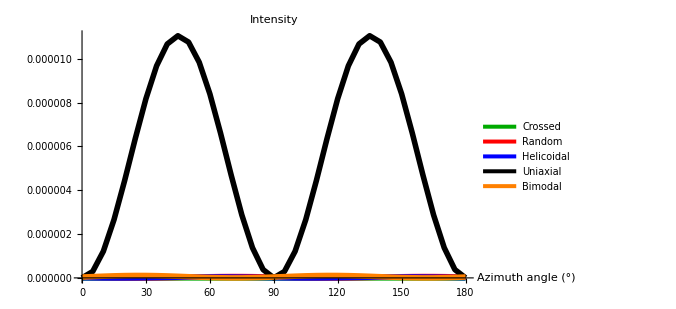
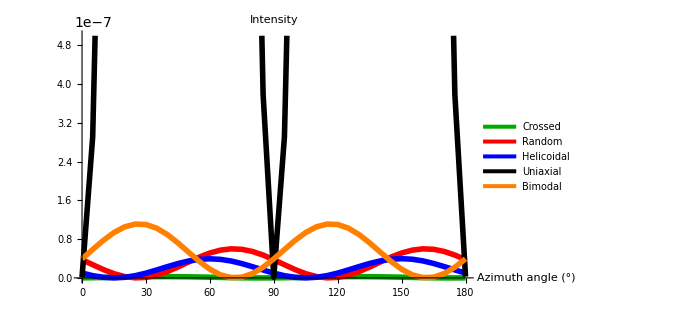

```mathematica
(* Check plots *)
{ListPlot[{clAng,raAng,heAng,unAng,biAng},PlotStyle->{{Darker[Green],Thickness[0.008]},{Red,Thickness[0.008]},{Blue,Thickness[0.008]},{Black,Thickness[0.008]},{Orange,Thickness[0.008]}},Ticks->{Table[30i,{i,0,6}],Automatic},PlotRange->All,ImageSize->500,AxesLabel->{"  Azimuth angle (°)",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},PlotLabel->Style["Intensity",20,Black,Bold],Joined->True,PlotLegends->{"Crossed","Random","Helicoidal","Uniaxial","Bimodal"}],
ListPlot[{clAng,raAng,heAng,unAng,biAng},PlotStyle->{{Darker[Green],Thickness[0.008]},{Red,Thickness[0.008]},{Blue,Thickness[0.008]},{Black,Thickness[0.008]},{Orange,Thickness[0.008]}},Ticks->{Table[30i,{i,0,6}],Automatic},PlotRange->{All,{0,5*10^-7}},ImageSize->500,AxesLabel->{"  Azimuth angle (°)",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},PlotLabel->Style["Intensity",20,Black,Bold],Joined->True,PlotLegends->{"Crossed","Random","Helicoidal","Uniaxial","Bimodal"}]}
```

```mathematica
(* Combine generated data *)
clAng2=Transpose[clAng];
raAng2=Transpose[raAng];
heAng2=Transpose[heAng];
unAng2=Transpose[unAng];
biAng2=Transpose[biAng];
b1={clAng2[[1]],clAng2[[2]],raAng2[[2]],heAng2[[2]],unAng2[[2]],biAng2[[2]]};
b1=Abs[b1];
b1=b1//Transpose;
b1//MatrixForm;

(* Data exportation *)
name=CurrentValue[EvaluationNotebook[],{"NotebookFileName"}];
name=StringDrop[name,-3];
time=TextString[TimeObject[]];
text1=StringTake[time,2];
text2=StringTake[time,{4,5}];
text3=StringTake[time,-2];
time2=ToExpression["text1"]<>ToString["."]<>ToExpression["text2"]<>ToString["."]<>ToExpression["text3"]
Export[NotebookDirectory[]<>ToExpression["name"]<>ToExpression["time2"]<>ToString["_"]<>"CRHUB.xlsx",b1];
```

22.27.42